# Model-based evaluation of school- and non-school-related interventions to control the COVID-19 pandemic

## Clearing memory

```mathematica
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
```

## Number of variables in the model Number of equations = number of age groups x number of variables =========== S - susceptible E - exposed I - infectious (3 infectious compartments) R - recovered H - hospitalized =========== Model equations Population size per age group Total population size Force of infection

## Number of age groups Age groups numbered

## Model variables Variables: matrix form

```mathematica
NumAgeGroups = 10
AgeGroups= Table[k, {k, 1, NumAgeGroups}]
NumInfStages=3;

TotNumVariables=4+NumInfStages;
VarNumbers= Table[j, {j, 1, TotNumVariables}]
EqNumbers=Table[k,{k,1,NumAgeGroups TotNumVariables}]

Table[
{eq[Intervention_][1,k]:=Subscript[S,k]'[t]== - Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t],
eq[Intervention_][2,k]:=Subscript[EE,k]'[t]== Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t]-α Subscript[EE,k][t],
eq[Intervention_][3,k]:=Subscript[II,k,1]'[t]== α Subscript[EE,k][t]-(NumInfStages γ+Subscript[ν,k]) Subscript[II,k,1][t],
eq[Intervention_][4,k]:=Subscript[II,k,2]'[t]==NumInfStages γ Subscript[II,k,1][t]-(NumInfStages γ +Subscript[ν,k]) Subscript[II,k,2][t],
eq[Intervention_][5,k]:=Subscript[II,k,NumInfStages]'[t]==NumInfStages γ Subscript[II,k,2][t]-(NumInfStages γ +Subscript[ν,k]) Subscript[II,k,NumInfStages][t],
eq[Intervention_][2+NumInfStages+1,k]:=Subscript[R,k]'[t]== NumInfStages γ Subscript[II,k,NumInfStages][t],
eq[Intervention_][2+NumInfStages+2,k]:=Subscript[H,k]'[t]==Subscript[ν,k] Sum[Subscript[II,k,p][t],{p,1,NumInfStages}]},{k,AgeGroups}];

(*Table[Subscript[NN,k][t]=(Subscript[S,k][t]+Subscript[EE,k][t]+Sum[Subscript[II,k,p][t],{p,1,NumInfStages}]+Subscript[R,k][t]+Subscript[H,k][t]),{k,AgeGroups}];*)

NNtot=Sum[Subscript[NN,k],{k,AgeGroups}];

Table[Subscript[λ,k][Intervention_/;Intervention=="Estimation"][t]= ϵ Sum[((1-1/(1+Exp[-KK (t-x0)])) Subscript[c,{k,l}]+1/(1+Exp[-KK (t-x0)]) ζ Subscript[d,{k,l}]) Sum[Subscript[II,l,p][t],{p,1,NumInfStages}]/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}];

Table[Subscript[λ,k][Intervention_/;Intervention=="Without Social Distancing"][t]= ϵ Sum[Subscript[c,{k,l}] Sum[Subscript[II,l,p][t],{p,1,NumInfStages}]/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}];

Table[Subscript[λ,k][Intervention_/;Intervention=="Full Social Distancing"][t]= ϵ Sum[ζ Subscript[d,{k,l}] Sum[Subscript[II,l,p][t],{p,1,NumInfStages}]/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}];

Table[Subscript[λ,k][Intervention_/;Intervention=="Relaxation with Schools"][t]= ϵ Sum[
(pp ζ Subscript[d,{k,l}]+(1-pp) κ (Subscript[c,{k,l}]-Subscript[s,{k,l}])+ω Subscript[s,{k,l}]) Subscript[II,l][t]/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}];

Table[Subscript[λ,k][Intervention_/;Intervention=="Relaxation with Schools 1"][t]= ϵ Sum[
(pp ζ Subscript[d,{k,l}]+(1-pp) κ (Subscript[c,{k,l}]-Subscript[s,{k,l}])+ω Subscript[s1,{k,l}]+Subscript[s,{k,l}]-Subscript[s1,{k,l}]) Subscript[II,l][t]/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}];

Table[Subscript[λ,k][Intervention_/;Intervention=="Relaxation with Schools 2"][t]= ϵ Sum[
(pp ζ Subscript[d,{k,l}]+(1-pp) κ (Subscript[c,{k,l}]-Subscript[s,{k,l}])+ω Subscript[s2,{k,l}]+Subscript[s,{k,l}]-Subscript[s2,{k,l}]) Subscript[II,l][t]/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}];

Table[Subscript[λ,k][Intervention_/;Intervention=="Relaxation with Schools 3"][t]= ϵ Sum[
(pp ζ Subscript[d,{k,l}]+(1-pp) κ (Subscript[c,{k,l}]-Subscript[s,{k,l}])+ω Subscript[s3,{k,l}]+Subscript[s,{k,l}]-Subscript[s3,{k,l}]) Subscript[II,l][t]/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}];

Eqs[Intervention_]:=Table[eq[Intervention][j,k],{j,TotNumVariables},{k,AgeGroups}]

TableForm[Eqs[Intervention]]

EqsList[Intervention_]:=Flatten[Flatten[Eqs[Intervention]]];

Total[EqsList[Intervention]⟦All,2⟧]//Simplify

varsS=Table[Subscript[S,k][t],{k,AgeGroups}];
varsEE=Table[Subscript[EE,k][t],{k,AgeGroups}];
varsII=Table[Subscript[II,k,p][t],{p,1,NumInfStages},{k,AgeGroups}];
varsR=Table[Subscript[R,k][t],{k,AgeGroups}];
varsH=Table[Subscript[H,k][t],{k,AgeGroups}];

Table[Subscript[II,k][t]=Sum[Subscript[II,k,p][t],{p,1,NumInfStages}],{k,AgeGroups}];

totS=Total[Total[varsS]];
totEE=Total[Total[varsEE]];
totII=Total[Total[varsII]];
totR=Total[Total[varsR]];
totH=Total[Total[varsH]];

totVars={totS,totEE,totII,totR,totH};

Vars=Join[varsS,varsEE,varsII,varsR,varsH];
VarsList=Flatten[Vars];
```

10

{1,2,3,4,5,6,7,8,9,10}

{1,2,3,4,5,6,7}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70}

S_1'[t]==-β_1 S_1[t] λ_1[Intervention][t] | S_2'[t]==-β_2 S_2[t] λ_2[Intervention][t] | S_3'[t]==-β_3 S_3[t] λ_3[Intervention][t] | S_4'[t]==-β_4 S_4[t] λ_4[Intervention][t] | S_5'[t]==-β_5 S_5[t] λ_5[Intervention][t] | S_6'[t]==-β_6 S_6[t] λ_6[Intervention][t] | S_7'[t]==-β_7 S_7[t] λ_7[Intervention][t] | S_8'[t]==-β_8 S_8[t] λ_8[Intervention][t] | S_9'[t]==-β_9 S_9[t] λ_9[Intervention][t] | S_10'[t]==-β_10 S_10[t] λ_10[Intervention][t]
EE_1'[t]==-α EE_1[t]+β_1 S_1[t] λ_1[Intervention][t] | EE_2'[t]==-α EE_2[t]+β_2 S_2[t] λ_2[Intervention][t] | EE_3'[t]==-α EE_3[t]+β_3 S_3[t] λ_3[Intervention][t] | EE_4'[t]==-α EE_4[t]+β_4 S_4[t] λ_4[Intervention][t] | EE_5'[t]==-α EE_5[t]+β_5 S_5[t] λ_5[Intervention][t] | EE_6'[t]==-α EE_6[t]+β_6 S_6[t] λ_6[Intervention][t] | EE_7'[t]==-α EE_7[t]+β_7 S_7[t] λ_7[Intervention][t] | EE_8'[t]==-α EE_8[t]+β_8 S_8[t] λ_8[Intervention][t] | EE_9'[t]==-α EE_9[t]+β_9 S_9[t] λ_9[Intervention][t] | EE_10'[t]==-α EE_10[t]+β_10 S_10[t] λ_10[Intervention][t]
II_(1,1)'[t]==α EE_1[t]-(3 γ+ν_1) II_(1,1)[t] | II_(2,1)'[t]==α EE_2[t]-(3 γ+ν_2) II_(2,1)[t] | II_(3,1)'[t]==α EE_3[t]-(3 γ+ν_3) II_(3,1)[t] | II_(4,1)'[t]==α EE_4[t]-(3 γ+ν_4) II_(4,1)[t] | II_(5,1)'[t]==α EE_5[t]-(3 γ+ν_5) II_(5,1)[t] | II_(6,1)'[t]==α EE_6[t]-(3 γ+ν_6) II_(6,1)[t] | II_(7,1)'[t]==α EE_7[t]-(3 γ+ν_7) II_(7,1)[t] | II_(8,1)'[t]==α EE_8[t]-(3 γ+ν_8) II_(8,1)[t] | II_(9,1)'[t]==α EE_9[t]-(3 γ+ν_9) II_(9,1)[t] | II_(10,1)'[t]==α EE_10[t]-(3 γ+ν_10) II_(10,1)[t]
II_(1,2)'[t]==3 γ II_(1,1)[t]-(3 γ+ν_1) II_(1,2)[t] | II_(2,2)'[t]==3 γ II_(2,1)[t]-(3 γ+ν_2) II_(2,2)[t] | II_(3,2)'[t]==3 γ II_(3,1)[t]-(3 γ+ν_3) II_(3,2)[t] | II_(4,2)'[t]==3 γ II_(4,1)[t]-(3 γ+ν_4) II_(4,2)[t] | II_(5,2)'[t]==3 γ II_(5,1)[t]-(3 γ+ν_5) II_(5,2)[t] | II_(6,2)'[t]==3 γ II_(6,1)[t]-(3 γ+ν_6) II_(6,2)[t] | II_(7,2)'[t]==3 γ II_(7,1)[t]-(3 γ+ν_7) II_(7,2)[t] | II_(8,2)'[t]==3 γ II_(8,1)[t]-(3 γ+ν_8) II_(8,2)[t] | II_(9,2)'[t]==3 γ II_(9,1)[t]-(3 γ+ν_9) II_(9,2)[t] | II_(10,2)'[t]==3 γ II_(10,1)[t]-(3 γ+ν_10) II_(10,2)[t]
II_(1,3)'[t]==3 γ II_(1,2)[t]-(3 γ+ν_1) II_(1,3)[t] | II_(2,3)'[t]==3 γ II_(2,2)[t]-(3 γ+ν_2) II_(2,3)[t] | II_(3,3)'[t]==3 γ II_(3,2)[t]-(3 γ+ν_3) II_(3,3)[t] | II_(4,3)'[t]==3 γ II_(4,2)[t]-(3 γ+ν_4) II_(4,3)[t] | II_(5,3)'[t]==3 γ II_(5,2)[t]-(3 γ+ν_5) II_(5,3)[t] | II_(6,3)'[t]==3 γ II_(6,2)[t]-(3 γ+ν_6) II_(6,3)[t] | II_(7,3)'[t]==3 γ II_(7,2)[t]-(3 γ+ν_7) II_(7,3)[t] | II_(8,3)'[t]==3 γ II_(8,2)[t]-(3 γ+ν_8) II_(8,3)[t] | II_(9,3)'[t]==3 γ II_(9,2)[t]-(3 γ+ν_9) II_(9,3)[t] | II_(10,3)'[t]==3 γ II_(10,2)[t]-(3 γ+ν_10) II_(10,3)[t]
R_1'[t]==3 γ II_(1,3)[t] | R_2'[t]==3 γ II_(2,3)[t] | R_3'[t]==3 γ II_(3,3)[t] | R_4'[t]==3 γ II_(4,3)[t] | R_5'[t]==3 γ II_(5,3)[t] | R_6'[t]==3 γ II_(6,3)[t] | R_7'[t]==3 γ II_(7,3)[t] | R_8'[t]==3 γ II_(8,3)[t] | R_9'[t]==3 γ II_(9,3)[t] | R_10'[t]==3 γ II_(10,3)[t]
H_1'[t]==ν_1 (II_(1,1)[t]+II_(1,2)[t]+II_(1,3)[t]) | H_2'[t]==ν_2 (II_(2,1)[t]+II_(2,2)[t]+II_(2,3)[t]) | H_3'[t]==ν_3 (II_(3,1)[t]+II_(3,2)[t]+II_(3,3)[t]) | H_4'[t]==ν_4 (II_(4,1)[t]+II_(4,2)[t]+II_(4,3)[t]) | H_5'[t]==ν_5 (II_(5,1)[t]+II_(5,2)[t]+II_(5,3)[t]) | H_6'[t]==ν_6 (II_(6,1)[t]+II_(6,2)[t]+II_(6,3)[t]) | H_7'[t]==ν_7 (II_(7,1)[t]+II_(7,2)[t]+II_(7,3)[t]) | H_8'[t]==ν_8 (II_(8,1)[t]+II_(8,2)[t]+II_(8,3)[t]) | H_9'[t]==ν_9 (II_(9,1)[t]+II_(9,2)[t]+II_(9,3)[t]) | H_10'[t]==ν_10 (II_(10,1)[t]+II_(10,2)[t]+II_(10,3)[t])

0

## Parameters of the model

## Importing contact data

## Contact rates c_{k,l}^{i,j}, 1/day

Imported demography 10 age groups

{866062.,917442.,2.00833×10^6,2.20179×10^6,2.1082×10^6,2.26111×10^6,2.50839×10^6,2.08991×10^6,1.52211×10^6,798820.}

School Matrix PLOS

(0.298862 | 0.0354444 | 4.65442×10^-15 | 0.0237057 | 0.0389781 | 0.00429861 | 0.00869807 | 1.25022×10^-60 | 2.53671×10^-126 | 3.32888×10^-126
0.136356 | 8.50941 | 0.37415 | 0.0853103 | 0.122278 | 0.105489 | 0.060803 | 0.00567744 | 1.36803×10^-88 | 4.35632×10^-122
0.00180232 | 0.314545 | 8.12674 | 0.0596786 | 0.153752 | 0.140146 | 0.0613046 | 7.8008×10^-47 | 1.28277×10^-116 | 1.68335×10^-116
7.79311×10^-44 | 4.90305×10^-50 | 0.0992463 | 0.0795021 | 0.0134103 | 0.00711065 | 2.63016×10^-47 | 1.07652×10^-84 | 2.31248×10^-110 | 5.72667×10^-119
0.0216067 | 0.73618 | 0.268035 | 0.0143028 | 0.0986895 | 0.262908 | 0.0416335 | 0.0057957 | 8.37962×10^-117 | 2.2927×10^-117
4.09379×10^-88 | 1.2832×10^-65 | 1.78748×10^-72 | 1.09604×10^-67 | 1.24072×10^-41 | 9.99714×10^-53 | 5.86252×10^-60 | 2.42887×10^-97 | 2.03293×10^-115 | 1.53062×10^-118
5.09576×10^-73 | 8.14519×10^-91 | 1.29796×10^-101 | 0.23598 | 0.0771389 | 0.192607 | 0.108856 | 1.54368×10^-93 | 1.1187×10^-114 | 3.16381×10^-120
0.0247814 | 5.2402×10^-95 | 1.33426×10^-103 | 1.03097×10^-104 | 6.95884×10^-111 | 9.55984×10^-94 | 1.35563×10^-89 | 1.32327×10^-108 | 1.55132×10^-115 | 5.77427×10^-119
3.77973×10^-105 | 1.29077×10^-124 | 1.6824×10^-114 | 7.69243×10^-115 | 5.49707×10^-115 | 1.65962×10^-86 | 0.0330387 | 1.05821×10^-100 | 1.89949×10^-116 | 8.39244×10^-119
2.60991×10^-129 | 3.22755×10^-124 | 1.65098×10^-114 | 4.46923×10^-117 | 1.326×10^-117 | 4.14985×10^-86 | 6.19264×10^-80 | 4.71072×10^-122 | 2.27025×10^-117 | 1.1502×10^-122)

{10,10}

All Locations Matrix PLOS

(2.04815 | 0.861782 | 0.222193 | 0.241948 | 2.29433 | 0.461263 | 0.619421 | 0.457434 | 0.0000671253 | 3.28154×10^-71
0.82528 | 11.2353 | 1.24475 | 0.429128 | 1.5513 | 1.6087 | 0.385398 | 0.136651 | 0.169065 | 0.0844112
0.159222 | 0.880793 | 14.3168 | 1.1033 | 2.33673 | 1.79543 | 0.735486 | 0.0713695 | 0.102978 | 4.3971×10^-21
0.298128 | 0.0938629 | 0.481364 | 4.53641 | 4.03765 | 1.80521 | 1.48314 | 0.09824 | 0.0246088 | 0.0321204
1.21835 | 1.44192 | 3.19644 | 2.02138 | 6.92591 | 6.72971 | 1.70071 | 0.261333 | 0.221748 | 0.16638
0.189882 | 0.658752 | 1.30277 | 2.75367 | 4.07193 | 6.48731 | 2.29621 | 0.310311 | 0.117097 | 0.0000111378
5.81316×10^-18 | 0.137884 | 0.661838 | 3.29636 | 1.95132 | 2.59565 | 2.80469 | 0.955428 | 0.0433354 | 0.0512386
0.151636 | 0.0945634 | 0.23717 | 0.571323 | 1.09858 | 0.812333 | 1.36377 | 1.86011 | 0.640971 | 0.116985
0.0158867 | 0.0440762 | 0.117879 | 0.324471 | 0.415943 | 0.84027 | 0.689867 | 1.02647 | 1.64291 | 0.50964
0.0397245 | 0.110212 | 0.29461 | 0.363302 | 0.507207 | 0.728908 | 0.533967 | 0.566205 | 1.10435 | 0.890238)

{10,10}

Factor Matrix PLOS

(0.145918 | 0.0411292 | 2.09477×10^-14 | 0.0979787 | 0.0169889 | 0.00931922 | 0.0140423 | 2.73311×10^-60 | 3.77907×10^-122 | 1.01443×10^-55
0.165224 | 0.757379 | 0.300583 | 0.198799 | 0.078823 | 0.0655739 | 0.157767 | 0.041547 | 8.09171×10^-88 | 5.16083×10^-121
0.0113195 | 0.357115 | 0.567638 | 0.0540912 | 0.065798 | 0.0780571 | 0.0833525 | 1.09302×10^-45 | 1.24567×10^-115 | 3.82833×10^-96
2.61402×10^-43 | 5.22363×10^-49 | 0.206177 | 0.0175253 | 0.00332132 | 0.00393896 | 1.77337×10^-47 | 1.09581×10^-83 | 9.39698×10^-109 | 1.78287×10^-117
0.0177344 | 0.510555 | 0.0838543 | 0.00707577 | 0.0142493 | 0.0390667 | 0.0244801 | 0.0221775 | 3.77888×10^-116 | 1.37798×10^-116
2.15597×10^-87 | 1.94793×10^-65 | 1.37206×10^-72 | 3.98028×10^-68 | 3.04701×10^-42 | 1.54103×10^-53 | 2.55313×10^-60 | 7.82723×10^-97 | 1.73611×10^-114 | 1.37425×10^-113
8.7659×10^-56 | 5.90728×10^-90 | 1.96114×10^-101 | 0.0715881 | 0.0395316 | 0.0742039 | 0.038812 | 1.6157×10^-93 | 2.5815×10^-113 | 6.17467×10^-119
0.163427 | 5.54147×10^-94 | 5.62574×10^-103 | 1.80453×10^-104 | 6.33437×10^-111 | 1.17684×10^-93 | 9.94035×10^-90 | 7.11394×10^-109 | 2.42027×10^-115 | 4.93591×10^-118
2.37918×10^-103 | 2.9285×10^-123 | 1.42723×10^-113 | 2.37076×10^-114 | 1.32159×10^-114 | 1.9751×10^-86 | 0.0478914 | 1.03093×10^-100 | 1.15617×10^-116 | 1.64674×10^-118
6.57004×10^-128 | 2.9285×10^-123 | 5.60394×10^-114 | 1.23017×10^-116 | 2.61432×10^-117 | 5.69324×10^-86 | 1.15974×10^-79 | 8.31981×10^-122 | 2.05573×10^-117 | 1.29201×10^-122)

School Matrix Jantien

(0.509923 | 0.0587043 | 2.6502×10^-14 | 0.146597 | 0.0334267 | 0.0133644 | 0.0137183 | 1.57068×10^-60 | 7.50134×10^-123 | 6.19509×10^-57
0.221385 | 5.9645 | 1.05751 | 0.392538 | 0.158345 | 0.122979 | 0.171288 | 0.0236544 | 1.90454×10^-88 | 3.48838×10^-122
0.00619741 | 0.579168 | 5.32046 | 0.159022 | 0.124555 | 0.167211 | 0.11671 | 6.58757×10^-46 | 3.15471×10^-116 | 3.84406×10^-97
1.58218×10^-43 | 4.44461×10^-49 | 0.566607 | 0.0816856 | 0.00839501 | 0.00857882 | 3.0107×10^-47 | 8.56222×10^-84 | 3.18198×10^-109 | 3.75796×10^-118
0.0148456 | 0.464821 | 0.156057 | 0.0188096 | 0.0518703 | 0.101846 | 0.0422249 | 0.0201541 | 1.52838×10^-116 | 3.29496×10^-117
1.14451×10^-87 | 1.44053×10^-65 | 2.51418×10^-72 | 7.93256×10^-68 | 6.91151×10^-42 | 5.30124×10^-53 | 4.93612×10^-60 | 7.45303×10^-97 | 8.03792×10^-115 | 3.23073×10^-114
3.02042×10^-56 | 2.4096×10^-90 | 2.23805×10^-101 | 0.105965 | 0.056528 | 0.136691 | 0.0884984 | 1.91478×10^-93 | 1.3983×10^-113 | 1.83576×10^-119
0.0393126 | 1.40675×10^-94 | 3.27957×10^-103 | 1.45896×10^-104 | 5.66353×10^-111 | 1.26711×10^-93 | 1.39809×10^-89 | 1.33261×10^-108 | 2.21622×10^-115 | 1.9031×10^-118
2.98575×10^-104 | 4.64212×10^-124 | 5.2806×10^-114 | 1.25461×10^-114 | 7.94305×10^-115 | 1.56179×10^-86 | 0.0464994 | 1.42587×10^-100 | 2.30513×10^-116 | 1.31647×10^-118
4.57929×10^-129 | 2.40663×10^-124 | 1.48407×10^-114 | 7.31548×10^-117 | 1.677×10^-117 | 4.12668×10^-86 | 1.11572×10^-79 | 8.74681×10^-122 | 2.96698×10^-117 | 1.53138×10^-122)

All Locations Matrix Jantien

(3.49459 | 1.42731 | 1.26515 | 1.49621 | 1.96756 | 1.43407 | 0.976927 | 0.574687 | 0.198497 | 0.0610699
1.33991 | 7.87519 | 3.51819 | 1.97454 | 2.00887 | 1.87543 | 1.0857 | 0.56934 | 0.235369 | 0.0675934
0.547496 | 1.6218 | 9.37298 | 2.93988 | 1.893 | 2.14217 | 1.4002 | 0.602697 | 0.253254 | 0.100411
0.605267 | 0.850866 | 2.74815 | 4.661 | 2.52761 | 2.17794 | 1.69773 | 0.781362 | 0.338618 | 0.210781
0.837104 | 0.910422 | 1.86105 | 2.65831 | 3.6402 | 2.60697 | 1.72487 | 0.908763 | 0.404453 | 0.239114
0.530857 | 0.739517 | 1.83241 | 1.99297 | 2.26829 | 3.44006 | 1.93336 | 0.952193 | 0.462985 | 0.235091
0.344565 | 0.407904 | 1.1412 | 1.48021 | 1.42995 | 1.84211 | 2.28018 | 1.18511 | 0.54166 | 0.297305
0.240551 | 0.253858 | 0.582957 | 0.808495 | 0.894096 | 1.07671 | 1.40647 | 1.87324 | 0.915692 | 0.385562
0.125495 | 0.158515 | 0.369988 | 0.529201 | 0.601021 | 0.790737 | 0.970935 | 1.38309 | 1.99376 | 0.799441
0.0696997 | 0.0821797 | 0.264826 | 0.594672 | 0.641466 | 0.724839 | 0.962044 | 1.05132 | 1.44327 | 1.18527)

Plotting contact matrices

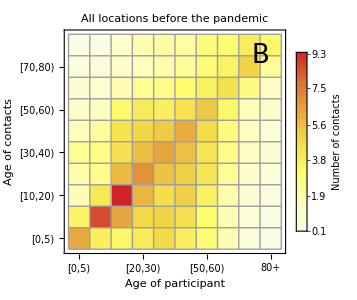

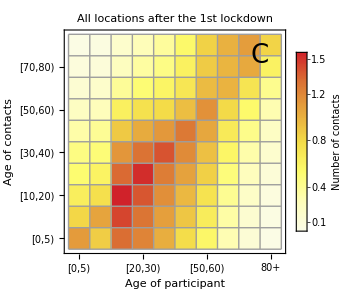

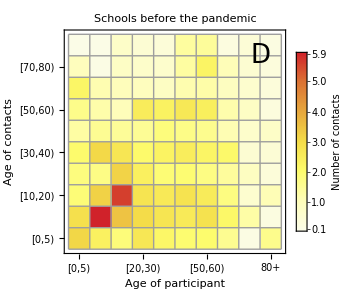

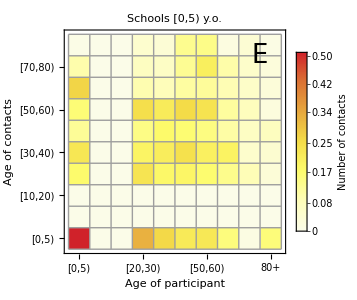

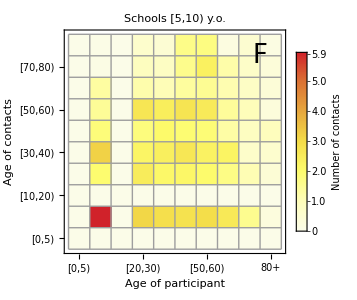

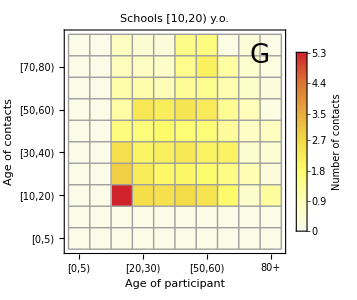

{{ManuscriptExit//Figures//Fig1B.pdf,ManuscriptExit//Figures//Fig1C.pdf,ManuscriptExit//Figures//Fig1D.pdf,ManuscriptExit//Figures//Fig1E.pdf,ManuscriptExit//Figures//Fig1F.pdf,ManuscriptExit//Figures//Fig1G.pdf},{ManuscriptExit//Figures//Fig1B.eps,ManuscriptExit//Figures//Fig1C.eps,ManuscriptExit//Figures//Fig1D.eps,ManuscriptExit//Figures//Fig1E.eps,ManuscriptExit//Figures//Fig1F.eps,ManuscriptExit//Figures//Fig1G.eps}}

```mathematica
SetDirectory["//Users//LynxGAV//Documents//Work//SecondWave//"];

Print[Style["Imported demography 10 age groups",18,Blue,"Text"]]
DemographyData=Flatten[Import["DEMOGRAPHY NL 10.xlsx"]]
Demography:=Table[Subscript[NN,k]-> DemographyData⟦k⟧,{k,AgeGroups}];

ContactDataAllLocationsBefore=Import["contactmatrix_unperturbed.csv"];
MatrixForm[ContactDataAllLocationsBefore];
ContactDataAllLocationsAfter=Import["contactmatrix_distancing.csv"];
ContactDataSchools=Import["contactmatrix_schools.xlsx"]⟦1⟧;
ContactDataAllLocations=Import["contactmatrix_alllocations.xlsx"]⟦1⟧;

(*===============================*)

(*Join[{v},m]*)
(*Join[List/@v,m,2]*)

(*Print[Style["Imported demography 17 age groups",18,Blue,"Text"]];*)
DemographyData17=Flatten[Import["DEMOGRAPHY NL 17.xlsx"]];

MatrixTransform17to10[ContactMatrix17_]:=Block[{ContactMatrix10},
ContactMatrix10=ContactMatrix17;
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10]; 

ContactMatrix10=Join[ContactMatrix10,{ContactMatrix10⟦16,All⟧}];
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10];

ContactMatrix10=Join[ContactMatrix10,List/@(ContactMatrix10⟦All,16⟧ DemographyData17⟦17⟧/DemographyData17⟦16⟧),2] ;
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10];

ContactMatrix10=Transpose[{ContactMatrix10⟦All,1⟧,ContactMatrix10⟦All,2⟧,ContactMatrix10⟦All,3⟧+ContactMatrix10⟦All,4⟧,ContactMatrix10⟦All,5⟧+ContactMatrix10⟦All,6⟧,ContactMatrix10⟦All,7⟧+ContactMatrix10⟦All,8⟧,ContactMatrix10⟦All,9⟧+ContactMatrix10⟦All,10⟧,ContactMatrix10⟦All,11⟧+ContactMatrix10⟦All,12⟧,ContactMatrix10⟦All,13⟧+ContactMatrix10⟦All,14⟧,ContactMatrix10⟦All,15⟧+ContactMatrix10⟦All,16⟧,ContactMatrix10⟦All,17⟧}];
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10];

ContactMatrix10={ContactMatrix10⟦1,All⟧,ContactMatrix10⟦2,All⟧,(ContactMatrix10⟦3,All⟧ DemographyData17⟦3⟧+ContactMatrix10⟦4,All⟧ DemographyData17⟦4⟧)/(DemographyData17⟦3⟧+DemographyData17⟦4⟧),(ContactMatrix10⟦5,All⟧ DemographyData17⟦5⟧+ContactMatrix10⟦6,All⟧ DemographyData17⟦6⟧)/(DemographyData17⟦5⟧+DemographyData17⟦6⟧),
(ContactMatrix10⟦7,All⟧ DemographyData17⟦7⟧+ContactMatrix10⟦8,All⟧ DemographyData17⟦8⟧)/(DemographyData17⟦7⟧+DemographyData17⟦8⟧),
(ContactMatrix10⟦9,All⟧ DemographyData17⟦9⟧+ContactMatrix10⟦10,All⟧ DemographyData17⟦10⟧)/(DemographyData17⟦9⟧+DemographyData17⟦10⟧),
(ContactMatrix10⟦11,All⟧ DemographyData17⟦11⟧+ContactMatrix10⟦12,All⟧ DemographyData17⟦12⟧)/(DemographyData17⟦11⟧+DemographyData17⟦12⟧),
(ContactMatrix10⟦13,All⟧ DemographyData17⟦13⟧+ContactMatrix10⟦14,All⟧ DemographyData17⟦14⟧)/(DemographyData17⟦13⟧+DemographyData17⟦14⟧),
(ContactMatrix10⟦15,All⟧ DemographyData17⟦15⟧+ContactMatrix10⟦16,All⟧ DemographyData17⟦16⟧)/(DemographyData17⟦15⟧+DemographyData17⟦16⟧),ContactMatrix10⟦17,All⟧};

Dimensions[ContactMatrix10];
ContactMatrix10//MatrixForm;
ContactMatrix10
]

Print[Style["School Matrix PLOS",18,Blue,"Text"]]
ContactDataSchools=MatrixTransform17to10[ContactDataSchools];
ContactDataSchools//MatrixForm
Dimensions[ContactDataSchools]
(*================================================*)

ContactDataAllLocationsBefore-ContactDataSchools;

(* One element is negative which means that there were more school contacts before the lockdown than the number of contacts in all locations *)

(*================================================*)

Print[Style["All Locations Matrix PLOS",18,Blue,"Text"]]
ContactDataAllLocations=MatrixTransform17to10[ContactDataAllLocations];
ContactDataAllLocations//MatrixForm
Dimensions[ContactDataAllLocations]
(*================================================*)

(*Ratio of the school contacts and all contacts *)

Print[Style["Factor Matrix PLOS",18,Blue,"Text"]]
FactorMatrix=ContactDataSchools/ContactDataAllLocations;
FactorMatrix//MatrixForm

Print[Style["School Matrix Jantien",18,Blue,"Text"]]
ContactDataSchoolsJantien=FactorMatrix*ContactDataAllLocationsBefore;
ContactDataSchoolsJantien//MatrixForm

Print[Style["All Locations Matrix Jantien",18,Blue,"Text"]]
ContactDataAllLocationsBefore//MatrixForm

ImSize=300;

Print[Style["Plotting contact matrices",18,Blue,"Text"]]

PlotContactMatrix[matrix_,label_,panel_]:=Show[MatrixPlot[matrix,FrameStyle->Opacity[0],FrameLabel->{Style["Age of contacts",Black,17,Opacity[1]],Style["Age of participant",Black,17,Opacity[1]]}, PlotLabel->Style[Row[{label}],Black,17],ClippingStyle->Automatic,DataReversed->{True,False},Mesh->True,Frame->True,FrameTicks->{{{1,"[0,5)"},{2,"[5,10)"},{3,"[10,20)"},{4,"[20,30)"},{5,"[30,40)"},{6,"[40,50)"},{7,"[50,60)"},{8,"[60,70)"},{9,"[70,80)"},{10,"80+"}},{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}}},FrameTicksStyle->{{{Black,17,Opacity[1]},None},{{Black,17,Opacity[1]},None}},ImageSize->ImSize,ColorFunction->"TemperatureMap",(*PlotTheme-> "Scientific",*)PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->"Number of\ncontacts",LabelStyle->Directive[Black,17,Opacity[1]]],{After,Top}]],Graphics[Text[StyleForm[panel,FontSize->26],{10*0.9,10*0.9}]]]

FigContactMatrixBefore=PlotContactMatrix[ContactDataAllLocationsBefore,"All locations\nbefore the pandemic","B"]
FigContactMatrixAfter=PlotContactMatrix[ContactDataAllLocationsAfter,"All locations\nafter the 1st lockdown","C"]
FigContactMatrixSchools=PlotContactMatrix[(*ContactDataSchools*)ContactDataSchoolsJantien,"Schools\nbefore the pandemic","D"]

rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]

ContactDataSchoolsJantien1=ContactDataSchoolsJantien;
ContactDataSchoolsJantien2=ContactDataSchoolsJantien;
ContactDataSchoolsJantien3=ContactDataSchoolsJantien;

Table[If[2≤k≤3||2≤l≤3,ContactDataSchoolsJantien1⟦k,l⟧=0],{k,1,NumAgeGroups},{l,1,NumAgeGroups}];
Table[If[1==k||k==3||1==l||l==3,ContactDataSchoolsJantien2⟦k,l⟧=0],{k,1,NumAgeGroups},{l,1,NumAgeGroups}];
Table[If[1≤k≤2||1≤l≤2,ContactDataSchoolsJantien3⟦k,l⟧=0],{k,1,NumAgeGroups},{l,1,NumAgeGroups}];


Table[ContactDataSchoolsJantien1⟦k,l⟧=(DemographyData⟦1⟧/(DemographyData⟦1⟧+DemographyData⟦2⟧+DemographyData⟦3⟧)) ContactDataSchoolsJantien1⟦k,l⟧,{k,4,NumAgeGroups},{l,4,NumAgeGroups}];
Table[ContactDataSchoolsJantien2⟦k,l⟧=(DemographyData⟦2⟧/(DemographyData⟦1⟧+DemographyData⟦2⟧+DemographyData⟦3⟧)) ContactDataSchoolsJantien2⟦k,l⟧,{k,4,NumAgeGroups},{l,4,NumAgeGroups}];
Table[ContactDataSchoolsJantien3⟦k,l⟧=(DemographyData⟦3⟧/(DemographyData⟦1⟧+DemographyData⟦2⟧+DemographyData⟦3⟧)) ContactDataSchoolsJantien3⟦k,l⟧,{k,4,NumAgeGroups},{l,4,NumAgeGroups}];

FigContactMatrixSchools1=PlotContactMatrix[(*ContactDataSchools*)ContactDataSchoolsJantien1,"Schools\n[0,5) y.o.","E"]
FigContactMatrixSchools2=PlotContactMatrix[(*ContactDataSchools*)ContactDataSchoolsJantien2,"Schools\n[5,10) y.o.","F"]
FigContactMatrixSchools3=PlotContactMatrix[(*ContactDataSchools*)ContactDataSchoolsJantien3,"Schools\n[10,20) y.o.","G"]

format={".pdf",".eps"};(*".jpg",".bmp",".png"*)
FigNames={"Fig1B","Fig1C","Fig1D","Fig1E","Fig1F","Fig1G"};
Figures={FigContactMatrixBefore,FigContactMatrixAfter,FigContactMatrixSchools,FigContactMatrixSchools1,FigContactMatrixSchools2,FigContactMatrixSchools3};
Table[Export[StringJoin["ManuscriptExit//Figures//",FigNames⟦j⟧,format⟦i⟧],Figures⟦j⟧],{i,1,Length[format]},{j,1,Length[FigNames]}]

ContactRates=
Flatten[Table[{Subscript[c,{k,l}]->ContactDataAllLocationsBefore⟦k,l⟧,Subscript[d,{k,l}]->ContactDataAllLocationsAfter⟦k,l⟧,Subscript[s,{k,l}]->(*ContactDataSchools*)ContactDataSchoolsJantien⟦k,l⟧,Subscript[s1,{k,l}]->ContactDataSchoolsJantien1⟦k,l⟧,Subscript[s2,{k,l}]->ContactDataSchoolsJantien2⟦k,l⟧,Subscript[s3,{k,l}]->ContactDataSchoolsJantien3⟦k,l⟧},{k,1,NumAgeGroups},{l,1,NumAgeGroups}]];
```

```mathematica
Print[Style["Imported estimated parameters: ganna_J3_wide-prior-alpha-gamma_DSD.csv",18,Blue,"Text"]]
EstimatesData=Import["ganna_J3_wide-prior-alpha-gamma_DSD.csv"];

Print[Style["Dimensions of the imported data",18,Blue,"Text"]]
Dimensions[EstimatesData]

Print[Style["Header of the imported data",18,Blue,"Text"]]
HeaderParameters=EstimatesData⟦1⟧

EstimatesData=Drop[EstimatesData,1];

ProbTransm[sample_]:=ϵ->EstimatesData⟦sample,1⟧;
zeta[sample_]:=ζ-> EstimatesData⟦sample,2⟧;
LatRate[sample_]:=α->EstimatesData⟦sample,23⟧;
RecRate[sample_]:=γ->EstimatesData⟦sample,3⟧;

(* hosp_classes=c(1,1,1,2,3,4,5,6,7,8) *)
(* susc_classes=c(1,1,1,2,2,2,2,3,3,3) *)

nu[sample_]:=Flatten[Join[Table[Subscript[ν,k]->EstimatesData⟦sample,4⟧,{k,1,3}],Table[Subscript[ν,k]->EstimatesData⟦sample,k+1⟧,{k,4,10}]]];

Inoculum[sample_]:=Flatten[Table[{Subscript[S0,k]-> 1-EstimatesData⟦sample,12⟧,Subscript[EE0,k]-> 0.5 EstimatesData⟦sample,12⟧,Table[Subscript[II0,k,p]-> 0.5/NumInfStages EstimatesData⟦sample,12⟧,{p,1,NumInfStages}],Subscript[R0,k]-> 0,Subscript[H0,k]-> 0},{k,AgeGroups}]];

Susceptibility[sample_]:=Flatten[Join[Table[Subscript[β,k]->EstimatesData⟦sample,24⟧ ,{k,1,3}],Table[Subscript[β,k]->EstimatesData⟦sample,25⟧ ,{k,4,7}],Table[Subscript[β,k]->EstimatesData⟦sample,26⟧ ,{k,8,10}]]]

x0logfact[sample_]:=x0-> EstimatesData⟦sample,21⟧; 
klogfact[sample_]:=KK-> EstimatesData⟦sample,22⟧;

Parameters[sample_]:=
Flatten[{ContactRates,ProbTransm[sample],LatRate[sample],RecRate[sample],nu[sample],Inoculum[sample],zeta[sample],Demography,klogfact[sample],x0logfact[sample],Susceptibility[sample]}];

rOverDisp[sample_]:=EstimatesData⟦sample,27⟧

ParametersMAP=Parameters[1460];

NumSamples=2000;
```

Imported estimated parameters: ganna_J3_wide-prior-alpha-gamma_DSD.csv

Dimensions of the imported data

{2001,27}

Header of the imported data

{epsilon,zeta,gamma,nu_short[1],nu_short[2],nu_short[3],nu_short[4],nu_short[5],nu_short[6],nu_short[7],nu_short[8],inoculum,p_short[1],p_short[2],p_short[3],p_short[4],p_short[5],p_short[6],p_short[7],p_short[8],x0,k,alpha,beta_short[1],beta_short[2],beta_short[3],r}

# Parameter estimates

{{Probability of transmission per contact,0.0746855,0.050501,0.117232},{Latent period (days),2.48797,1.61565,3.89696},{Reduction in probability of
transmission per contact (%),48.8361,23.8076,87.4434},{Infectious period (days),4.76844,2.68755,11.6995},{Inoculum,0.0000479975,0.0000267008,0.0000822408},{Susceptibility of [0,20) y.o. relative to 60+ y.o.,0.233285,0.195795,0.277301},{Susceptibility of [20,60) y.o. relative to 60+ y.o.,0.608409,0.501894,0.723863},{Midpoint value of the logistic function (days),28.0569,26.6312,29.2495},{Logistic growth rate (1/day),0.451386,0.288475,1.06008},{Overdispersion parameter,15.9723,11.8269,21.6353}}

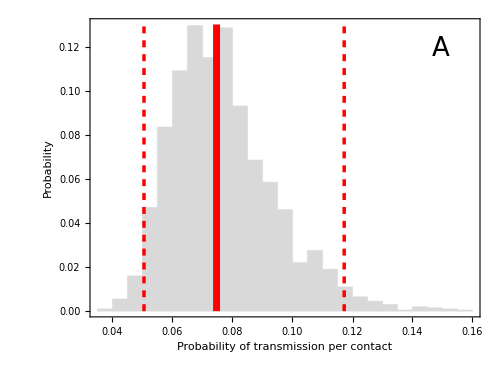
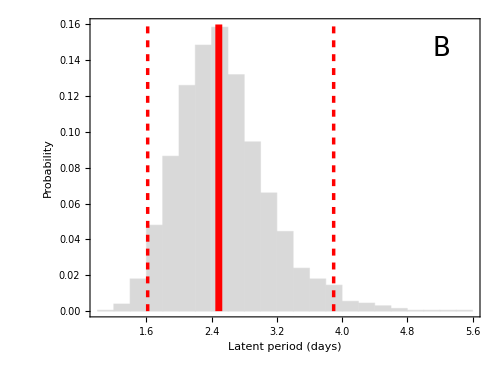
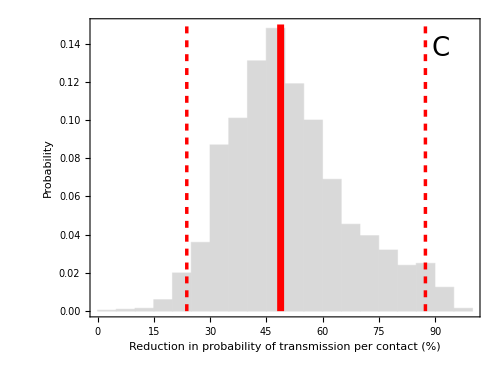
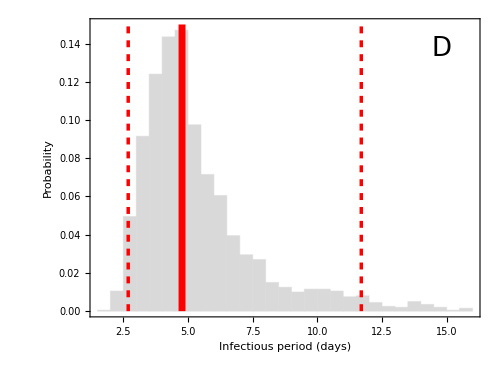
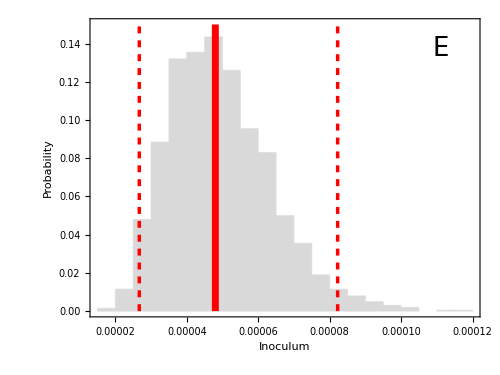
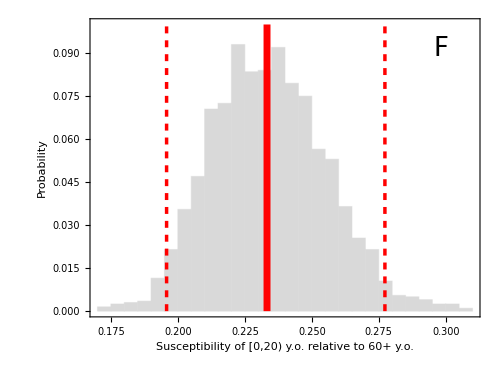
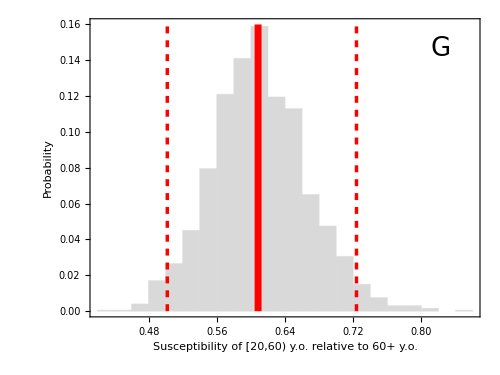
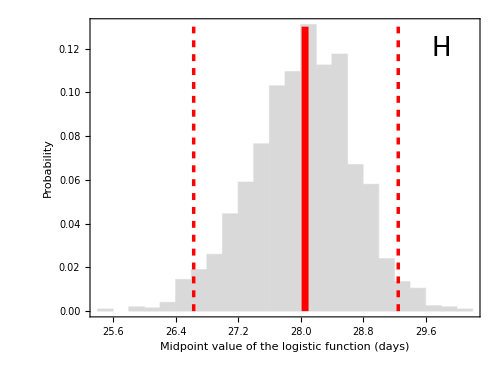

{{ManuscriptExit//Figures//FigS3A.pdf,ManuscriptExit//Figures//FigS3B.pdf,ManuscriptExit//Figures//FigS3C.pdf,ManuscriptExit//Figures//FigS3D.pdf,ManuscriptExit//Figures//FigS3E.pdf,ManuscriptExit//Figures//FigS3F.pdf,ManuscriptExit//Figures//FigS3G.pdf,ManuscriptExit//Figures//FigS3H.pdf,ManuscriptExit//Figures//FigS3I.pdf,ManuscriptExit//Figures//FigS3J.pdf},{ManuscriptExit//Figures//FigS3A.eps,ManuscriptExit//Figures//FigS3B.eps,ManuscriptExit//Figures//FigS3C.eps,ManuscriptExit//Figures//FigS3D.eps,ManuscriptExit//Figures//FigS3E.eps,ManuscriptExit//Figures//FigS3F.eps,ManuscriptExit//Figures//FigS3G.eps,ManuscriptExit//Figures//FigS3H.eps,ManuscriptExit//Figures//FigS3I.eps,ManuscriptExit//Figures//FigS3J.eps}}

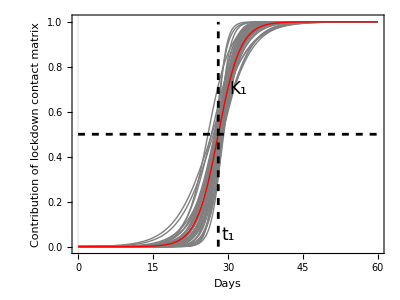

{ManuscriptExit//Figures//FigS1.pdf,ManuscriptExit//Figures//FigS1.eps}

```mathematica
AspRat=0.75; ImSize=400;

HistPlot[vals_,maxY_,xlab_,panel_]:=Show[Histogram[vals,20,"Probability",AspectRatio->0.75,ImageSize->500,AxesOrigin->{0,0},PlotRange->{Automatic,{0,All}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Probability",None},{xlab,None}},ChartStyle->LightGray],Graphics[{Thickness[0.01],Red,Line[{{Median[vals],0},{Median[vals],maxY}}]}],Graphics[{Thickness[0.005],Red,Dashed,Line[{{Quantile[vals,0.025],0},{Quantile[vals,0.025],maxY}}]}],Graphics[{Thickness[0.005],Red,Dashed,Line[{{Quantile[vals,0.975],0},{Quantile[vals,0.975],maxY}}]}],Graphics[Text[StyleForm[panel,FontSize->26],Scaled[{0.9,0.9}]]]]

vals={EstimatesData⟦All,1⟧,1/EstimatesData⟦All,23⟧,(1-EstimatesData⟦All,2⟧) 100,1/EstimatesData⟦All,3⟧,EstimatesData⟦All,12⟧,EstimatesData⟦All,24⟧,EstimatesData⟦All,25⟧,EstimatesData⟦All,21⟧,EstimatesData⟦All,22⟧,EstimatesData⟦All,27⟧};
maxY={0.13,0.16,0.15,0.15,0.15,0.1,0.16,0.13,0.5,0.17};
xlab={"Probability of transmission per contact","Latent period (days)","Reduction in probability of\ntransmission per contact (%)","Infectious period (days)","Inoculum","Susceptibility of [0,20) y.o. relative to 60+ y.o.","Susceptibility of [20,60) y.o. relative to 60+ y.o.","Midpoint value of the logistic function (days)","Logistic growth rate (1/day)","Overdispersion parameter"};
FigNames={"A","B","C","D","E","F","G","H","I","J"};

Table[{xlab⟦i⟧,Median[vals⟦i⟧],Quantile[vals⟦i⟧,0.025],Quantile[vals⟦i⟧,0.975]},{i,1,Length[vals]}]

Table[fig3[i]=HistPlot[vals⟦i⟧,maxY⟦i⟧,xlab⟦i⟧,FigNames⟦i⟧],{i,1,Length[vals]}]
Table[Export[StringJoin["ManuscriptExit//Figures//FigS3",FigNames⟦j⟧,format⟦i⟧],fig3[j]],{i,1,Length[format]},{j,1,Length[vals]}]

fig4=Show[Plot[Table[(1/(1+Exp[-KK (t-x0)]))/.{x0-> EstimatesData⟦sample,21⟧,KK->EstimatesData⟦sample,22⟧},{sample,1,NumSamples,50}],{t,0,60},GridLines->{{Median[EstimatesData⟦All,17⟧]},None},AxesOrigin->{0,0},PlotRange->{{0,60},{-0.01,1.01}},PlotStyle->{Gray,Thickness[0.0025]},AspectRatio->AspRat,ImageSize->ImSize,Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Contribution of lockdown contact matrix",None},{"Days",None}}],Plot[(1/(1+Exp[-KK (t-x0)]))/.{x0-> Median[EstimatesData⟦All,21⟧],KK->Median[EstimatesData⟦All,22⟧]},{t,0,60},GridLines->{{Median[EstimatesData⟦All,17⟧]},None},AxesOrigin->{0,0},PlotRange->{{0,60},{-0.01,1.01}},PlotStyle->{Red,Thick},AspectRatio->AspRat,ImageSize->ImSize,Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Contribution of lockdown contact matrix",None},{"Days",None}}],Graphics[{Thickness[0.005],Black,Dashed,Line[{{Median[EstimatesData⟦All,21⟧],0},{Median[EstimatesData⟦All,21⟧],1}}]}],Graphics[{Thickness[0.005],Black,Dashed,Line[{{0,0.5},{60,0.5}}]}],Graphics[Text[StyleForm["t_1",FontSize->17],{30,0.05}]],Graphics[Text[StyleForm["K_1",FontSize->17],{32,0.7}]]]

Table[Export[StringJoin["ManuscriptExit//Figures//FigS1",format⟦i⟧],fig4],{i,1,Length[format]}]
```

Probability of hospitalization

{[0,20) y.o.,[20,30) y.o.,[30,40) y.o.,[40,50) y.o.,[50,60) y.o.,[60,70) y.o.,[70,80) y.o.,80+ y.o}

{{[0,20) y.o.,0.000854132,0.000526077,0.00150627},{[20,30) y.o.,0.00102296,0.000738788,0.00165817},{[30,40) y.o.,0.00234369,0.00169156,0.00373363},{[40,50) y.o.,0.00590738,0.00430558,0.00950539},{[50,60) y.o.,0.0145832,0.0106127,0.0246465},{[60,70) y.o.,0.0167929,0.0112249,0.032389},{[70,80) y.o.,0.0295635,0.0193262,0.058015},{80+ y.o,0.0436691,0.0280402,0.0882233}}

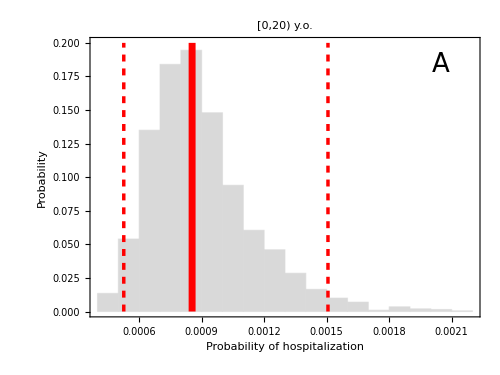
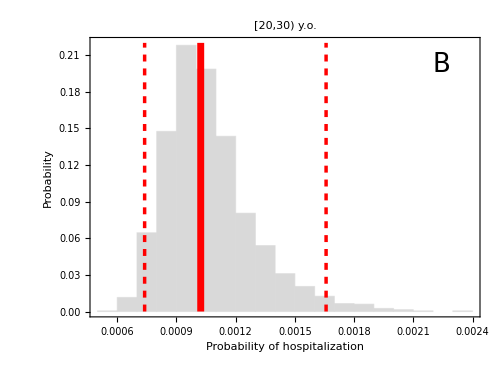
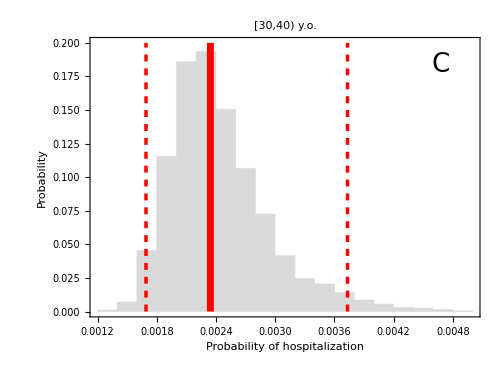
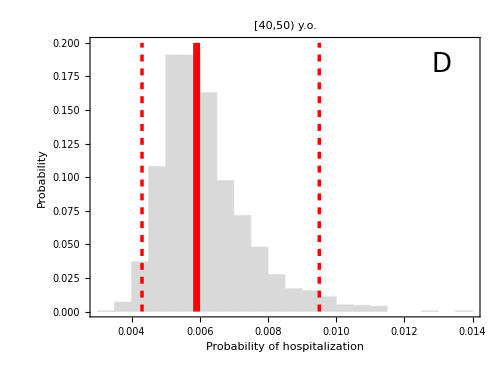
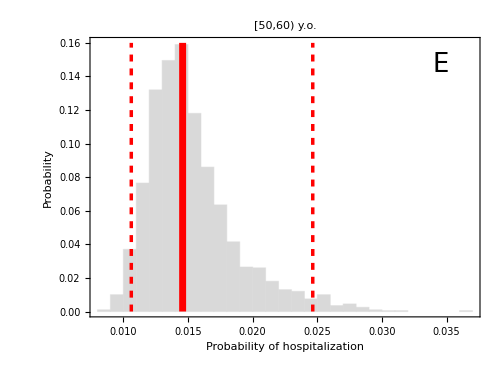
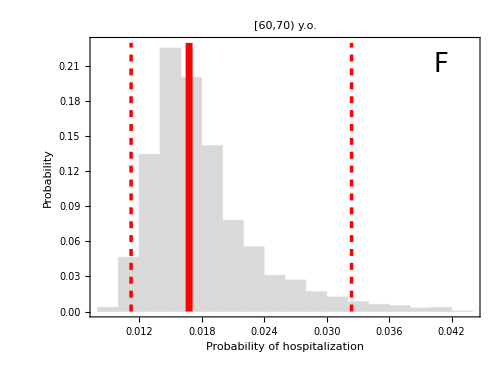
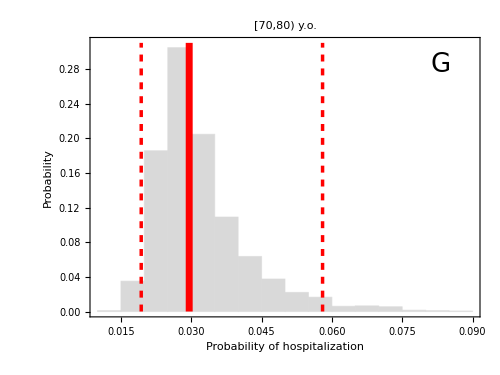
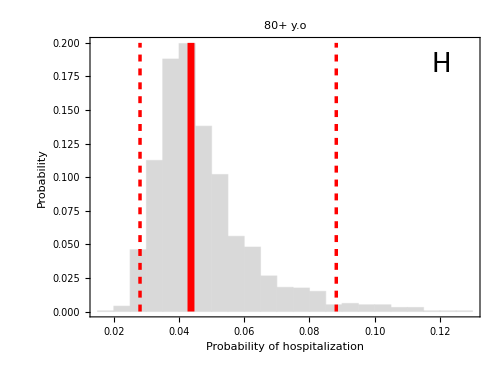

{{ManuscriptExit//Figures//FigS2A.pdf,ManuscriptExit//Figures//FigS2B.pdf,ManuscriptExit//Figures//FigS2C.pdf,ManuscriptExit//Figures//FigS2D.pdf,ManuscriptExit//Figures//FigS2E.pdf,ManuscriptExit//Figures//FigS2F.pdf,ManuscriptExit//Figures//FigS2G.pdf,ManuscriptExit//Figures//FigS2H.pdf},{ManuscriptExit//Figures//FigS2A.eps,ManuscriptExit//Figures//FigS2B.eps,ManuscriptExit//Figures//FigS2C.eps,ManuscriptExit//Figures//FigS2D.eps,ManuscriptExit//Figures//FigS2E.eps,ManuscriptExit//Figures//FigS2F.eps,ManuscriptExit//Figures//FigS2G.eps,ManuscriptExit//Figures//FigS2H.eps}}

```mathematica
HistPlotLabel[vals_,maxY_,xlab_,label_]:=Show[Histogram[vals,20,"Probability",AspectRatio->0.75,ImageSize->400,AxesOrigin->{0,0},PlotRange->{Automatic,{0,All}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Probability",None},{xlab,None}},ChartStyle->LightGray,PlotLabel->Style[Row[{label}],Black,17]],Graphics[{Thickness[0.01],Red,Line[{{Median[vals],0},{Median[vals],maxY}}]}],Graphics[{Thickness[0.005],Red,Dashed,Line[{{Quantile[vals,0.025],0},{Quantile[vals,0.025],maxY}}]}],Graphics[{Thickness[0.005],Red,Dashed,Line[{{Quantile[vals,0.975],0},{Quantile[vals,0.975],maxY}}]}]]

HistPlotLabelPanel[vals_,maxY_,xlab_,label_,panel_]:=Show[Histogram[vals,20,"Probability",AspectRatio->0.75,ImageSize->500,AxesOrigin->{0,0},PlotRange->{Automatic,{0,All}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Probability",None},{xlab,None}},ChartStyle->LightGray,PlotLabel->Style[Row[{label}],Black,17]],Graphics[{Thickness[0.01],Red,Line[{{Median[vals],0},{Median[vals],maxY}}]}],Graphics[{Thickness[0.005],Red,Dashed,Line[{{Quantile[vals,0.025],0},{Quantile[vals,0.025],maxY}}]}],Graphics[{Thickness[0.005],Red,Dashed,Line[{{Quantile[vals,0.975],0},{Quantile[vals,0.975],maxY}}]}],Graphics[Text[StyleForm[panel,FontSize->26],Scaled[{0.9,0.9}]]]]

vals=Table[EstimatesData⟦All,12+i⟧,{i,1,8}];
maxY={0.2,0.22,0.20,0.20,0.16,0.23,0.31,0.20};
xlab="Probability of hospitalization"
label={"[0,20) y.o.","[20,30) y.o.","[30,40) y.o.","[40,50) y.o.","[50,60) y.o.","[60,70) y.o.","[70,80) y.o.","80+ y.o"}

Table[{label⟦i⟧,Median[vals⟦i⟧],Quantile[vals⟦i⟧,0.025],Quantile[vals⟦i⟧,0.975]},{i,1,Length[vals]}]

FigNames={"A","B","C","D","E","F","G","H"};
Table[fig5[i]=HistPlotLabelPanel[vals⟦i⟧,maxY⟦i⟧,xlab,label⟦i⟧,FigNames⟦i⟧],{i,1,Length[vals]}]
Table[Export[StringJoin["ManuscriptExit//Figures//FigS2",FigNames⟦j⟧,format⟦i⟧],fig5[j]],{i,1,Length[format]},{j,1,Length[vals]}]
```

# Seroprevalence

Imported seroprevalence data: SeroData.csv

{{AgeClass,Positive,SampleSize,Day,Frac,Lower,Upper},{[0,5),2,208,30,0.00961538,0.00200334,0.0304851},{[5,10),2,158,30,0.0126582,0.0026395,0.0399826},{[10,20),8,291,30,0.0274914,0.0130809,0.0511995},{[20,30),17,394,30,0.0431472,0.0263127,0.0666503},{[30,40),19,463,30,0.0410367,0.0257317,0.0620476},{[40,50),13,460,30,0.0282609,0.0159314,0.0464864},{[50,60),9,463,30,0.0194384,0.00966065,0.0351745},{[60,70),8,404,30,0.019802,0.00940507,0.0370146},{[70,80),7,274,30,0.0255474,0.0114983,0.0495005},{[80,Inf),3,91,30,0.032967,0.00937078,0.0853575}}

Header of the imported data

{AgeClass,Positive,SampleSize,Day,Frac,Lower,Upper}

Imported simulated seroprevalence: SeroViolin.csv

{{[0,5),[5,10),[10,20),[20,30),[30,40),[40,50),[50,60),[60,70),[70,80),[80,Inf)},{0.00892798,0.0123433,0.0137634,0.0422015,0.0402836,0.036347,0.0280214,0.0332136,0.0303111,0.0283395},1998,{0.0111161,0.0164739,0.0179864,0.0370216,0.0351562,0.0317943,0.0245536,0.0346037,0.0322432,0.0298055}}
 |  |  |  |

Header of the imported data

{[0,5),[5,10),[10,20),[20,30),[30,40),[40,50),[50,60),[60,70),[70,80),[80,Inf)}

Median and quantiles, simulated seroprevalence

{{0.00900656,0.0127837,0.014156,0.0367397,0.0349735,0.0316043,0.0244201,0.0316457,0.0291871,0.0271129},{0.00662226,0.00925348,0.0103013,0.0292614,0.0278587,0.0251787,0.019458,0.0234767,0.0210727,0.0196093},{0.0123015,0.0180868,0.0197651,0.0451668,0.0431235,0.0388907,0.0301097,0.0419582,0.0401496,0.0371952}}

{866062.,917442.,2.00833×10^6,2.20179×10^6,2.1082×10^6,2.26111×10^6,2.50839×10^6,2.08991×10^6,1.52211×10^6,798820.}

0.0270521

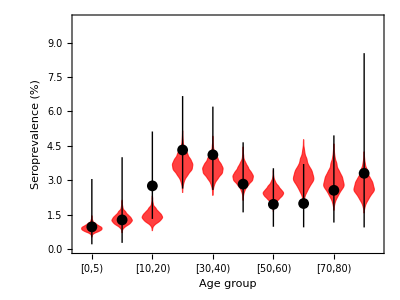

{ManuscriptExit//Figures//Fig4.pdf,ManuscriptExit//Figures//Fig4.eps}

Imported estimated hospitalization rates: HospRateViolin.csv

{{[0,5),[5,10),[10,20),[20,30),[30,40),[40,50),[50,60),[60,70),[70,80),[80,Inf)},{-3.67663,-3.67663,-3.67663,-3.65492,-3.2929,-2.91737,-2.51089,-2.42537,-2.17686,-2.0011},1998,{-3.73631,-3.73631,-3.73631,-3.64633,-3.27767,-2.84721,-2.45579,-2.46694,-2.19622,-2.04358}}
 |  |  |  |

Header of the imported data

{[0,5),[5,10),[10,20),[20,30),[30,40),[40,50),[50,60),[60,70),[70,80),[80,Inf)}

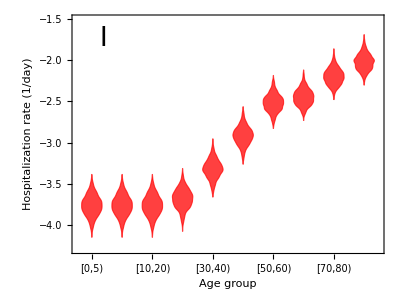

Imported estimated hospitalization probabilities: HospProbViolin.csv

{{V1,V2,V3,V4,V5,V6,V7,V8},{0.000930077,0.000977705,0.00224739,0.00531951,0.0134518,0.0163318,0.0285823,0.0422391},{0.000995332,0.00111152,0.00228845,0.00561099,0.0149836,0.016304,0.0333248,0.0448822},1995,{0.000700118,0.000870739,0.00202841,0.00480886,0.0111579,0.0128847,0.023106,0.0321755},{0.00107004,0.00131879,0.0024162,0.00671347,0.0150014,0.0141169,0.0222038,0.0295104},{0.000801122,0.000985383,0.00229979,0.00617244,0.0150652,0.014689,0.027054,0.0380143}}
 |  |  |  |

Header of the imported data

{V1,V2,V3,V4,V5,V6,V7,V8}

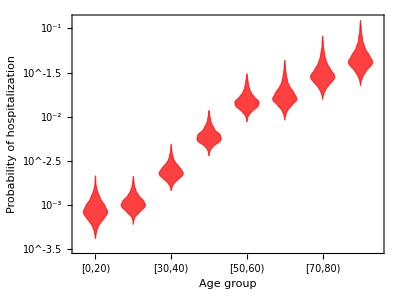

{ManuscriptExit//Figures//Fig3.pdf,ManuscriptExit//Figures//Fig3.eps}

```mathematica
Print[Style["Imported seroprevalence data: SeroData.csv",18,Blue,"Text"]]
SeroData=Import["SeroData.csv"]
Print[Style["Header of the imported data",18,Blue,"Text"]]
HeaderSeroData=SeroData⟦1⟧
SeroData=Drop[SeroData,1];
Needs["ErrorBarPlots`"]

Print[Style["Imported simulated seroprevalence: SeroViolin.csv",18,Blue,"Text"]]
SeroViolin=Import["SeroViolin.csv"]
Print[Style["Header of the imported data",18,Blue,"Text"]]
HeaderSeroViolin=SeroViolin⟦1⟧
SeroViolin=Drop[SeroViolin,1];

Print[Style["Median and quantiles, simulated seroprevalence",18,Blue,"Text"]]
{Median[SeroViolin], Quantile[SeroViolin,0.025],Quantile[SeroViolin,0.975]}

mediansero=Median[SeroViolin];
DemographyData

Sum[mediansero⟦i⟧ DemographyData⟦i⟧,{i,1,Length[DemographyData]}]/Total[DemographyData]

figsero=Show[DistributionChart[Table[SeroViolin⟦All,i⟧ 100,{i,1,Length[HeaderSeroViolin]}],ChartStyle->Directive[Red,Opacity[0.75]],AspectRatio->0.75,ImageSize->400,Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Seroprevalence (%)",None},{"Age group",None}},PlotRange->{All,{0,10}},PlotRangePadding->None],ErrorListPlot[Table[{{i,SeroData⟦i,5⟧ 100},ErrorBar[{SeroData⟦i,6⟧ 100-SeroData⟦i,5⟧100,SeroData⟦i,7⟧100-SeroData⟦i,5⟧100}]},{i,Length[SeroData]}],PlotRange->All,PlotStyle->{Black,Thickness[0.0025]}],FrameTicks->{{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}},Automatic},Frame-> {{True,False},{True,False}}]

Table[Export[StringJoin["ManuscriptExit//Figures//Fig4",format⟦i⟧],figsero],{i,1,Length[format]}]

Print[Style["Imported estimated hospitalization rates: HospRateViolin.csv",18,Blue,"Text"]]
HospRateViolin=Import["HospRateViolin.csv"]
Print[Style["Header of the imported data",18,Blue,"Text"]]
HeaderHospRateViolin=HospRateViolin⟦1⟧
HospRateViolin=Drop[HospRateViolin,1];

fighosprates=Show[DistributionChart[Table[HospRateViolin⟦All,i⟧,{i,1,Length[HeaderHospRateViolin]}],ChartStyle->Directive[Red,Opacity[0.75]],AspectRatio->0.75,ImageSize->400,Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Hospitalization rate (1/day)",None},{"Age group",None}},PlotRange->All,PlotRangePadding->None],Graphics[Text[StyleForm["I",FontSize->26],Scaled[{0.1,0.9}]]],FrameTicks->{{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}},Automatic}]

(*Table[Export[StringJoin["ManuscriptExit//Figures//Fig9_9",format⟦i⟧],fighosprates],{i,1,Length[format]}]*)


Print[Style["Imported estimated hospitalization probabilities: HospProbViolin.csv",18,Blue,"Text"]]
HospProbViolin=Import["HospProbViolin.csv"]
Print[Style["Header of the imported data",18,Blue,"Text"]]
HeaderHospProbViolin=HospProbViolin⟦1⟧
HospProbViolin=Drop[HospProbViolin,1];

fighospprob=Show[DistributionChart[Table[HospProbViolin⟦All,i⟧,{i,1,Length[HeaderHospProbViolin]}],ChartStyle->Directive[Red,Opacity[0.75]],AspectRatio->0.75,ImageSize->400,Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Probability of hospitalization",None},{"Age group",None}},PlotRange->{All,{-3.5,-0.9}},PlotRangePadding->None,ScalingFunctions->"Log10"],(*Graphics[Text[StyleForm["I",FontSize->26],Scaled[{0.1,0.9}]]],*)FrameTicks->{{{1,Rotate["[0,20)",Pi/2]},{2,Rotate["[20,30)",Pi/2]},{3,Rotate["[30,40)",Pi/2]},{4,Rotate["[40,50)",Pi/2]},{5,Rotate["[50,60)",Pi/2]},{6,Rotate["[60,70)",Pi/2]},{7,Rotate["[70,80)",Pi/2]},{8,Rotate["80+",Pi/2]}},{{-1,"10^-1"},{-2,"10^-2"},{-3,"10^-3"}}}]

(*FrameTicks->{{{{Log[0.001],"0.001"},{Log[0.01],"0.01"}},None},{None,None}}*)

Table[Export[StringJoin["ManuscriptExit//Figures//Fig3",format⟦i⟧],fighospprob],{i,1,Length[format]}]
```

# R_0 calculation Jacobian Disease free steady state Transmission matrix Transition matrix

```mathematica
EqNumbersR0=EqNumbers⟦NumAgeGroups+1;;2 NumAgeGroups+NumAgeGroups NumInfStages⟧;
DiseaseFreeState=Flatten[Table[{Subscript[S,k][t]->Subscript[NN,k](*-Subscript[R0,k] Subscript[NN,k]*),Subscript[EE,k][t]->0,Table[Subscript[II,k,p][t]->0,{p,1,NumInfStages}],Subscript[R,k][t]->0(*Subscript[R0,k] Subscript[NN,k]*),Subscript[H,k][t]->0},{k,AgeGroups}]];

PrintStats[vals_]:={Median[vals],Quantile[vals,0.025],Quantile[vals,0.975],Mean[vals],StandardDeviation[vals]};

formattable={".csv",".txt",".xls",".tsv"};

(* Table[Subscript[λ,k][Intervention_/;Intervention=="Relaxation with Schools"][t]= ϵ Sum[
(pp ζ Subscript[d,{k,l}]+(1-pp) κ (Subscript[c,{k,l}]-Subscript[s,{k,l}])+ ω Subscript[s,{k,l}]) Subscript[II,l][t]/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}]; *) 

(* p*zeta*D+(1-p)*kappa*(C-S)+omega*S *)

(* 
"Without Social Distancing"
"Full Social Distancing"
"Relaxation with Schools"
*)

Reff[Intervention_,omega_,kappa_,pfactor_]:=Block[{JacobAnalyt,JacobAnalytDiseaseFreeState,TransmissionMatrix,TransitionMatrix,Reffvals},
JacobAnalyt=Table[ D[EqsList[Intervention]⟦k,2⟧,VarsList⟦p⟧],{k,EqNumbersR0} ,{p,EqNumbersR0}];
JacobAnalytDiseaseFreeState=JacobAnalyt/.DiseaseFreeState;
TransmissionMatrix=ϵ Table[Coefficient[JacobAnalytDiseaseFreeState⟦k⟧⟦p⟧,ϵ],{k,1,Length[EqNumbersR0]} ,{p,1,Length[EqNumbersR0]}];
TransitionMatrix=JacobAnalytDiseaseFreeState-TransmissionMatrix;
(*Print[Style["Effective reproduction number",18,Blue,"Text"]];*)
Print[Style[Intervention,18,Blue,"Text"]];

Table[Re[Eigenvalues[(-TransmissionMatrix/.Join[Parameters[i],{ω-> omega,κ-> kappa,pp-> pfactor}]).Inverse[TransitionMatrix/.Join[Parameters[i],{ω-> omega,κ-> kappa,pp-> pfactor}]]]⟦1⟧],{i,1,NumSamples}]
]
```

R_e, Median, 2.5% Quantile, 97.5% Quantile, Mean, Standard Deviation

Without Social Distancing

{2.71011,2.15334,5.17942,2.92794,0.753901}

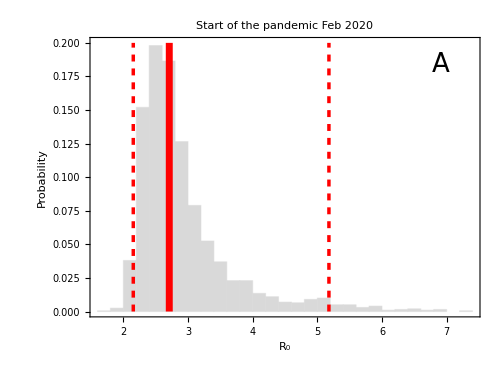

Full Social Distancing

{0.621729,0.286666,0.74167,0.59554,0.111353}

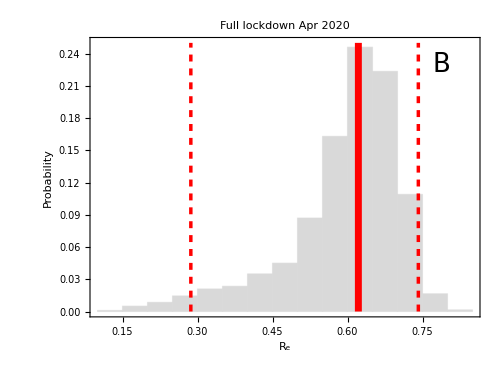

Relaxation with Schools

{1.30993,1.15096,2.07327,1.37861,0.232278}

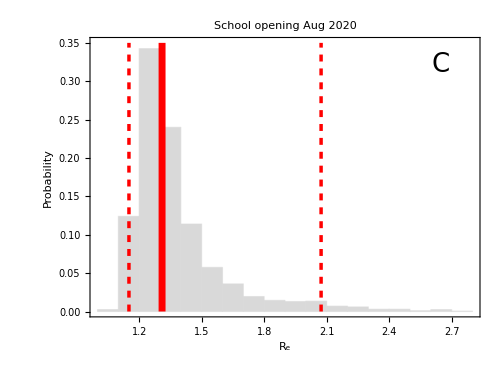

Relaxation with Schools

{1.00161,0.939767,1.33184,1.03158,0.101186}

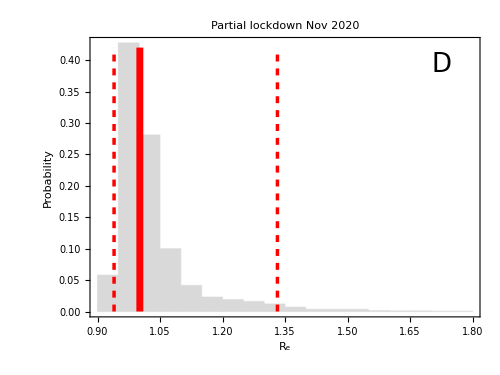

{{ManuscriptExit//Figures//FigS4A.pdf,ManuscriptExit//Figures//FigS4B.pdf,ManuscriptExit//Figures//FigS4C.pdf,ManuscriptExit//Figures//FigS4D.pdf},{ManuscriptExit//Figures//FigS4A.eps,ManuscriptExit//Figures//FigS4B.eps,ManuscriptExit//Figures//FigS4C.eps,ManuscriptExit//Figures//FigS4D.eps}}

```mathematica
Print[Style["R_e, Median, 2.5% Quantile, 97.5% Quantile, Mean, Standard Deviation",18,Blue,"Text"]]

Reffvals=Reff["Without Social Distancing",ω,κ,pp];
PrintStats[Reffvals]
fig6[1]=HistPlotLabelPanel[Reffvals,0.20,"R_0","Start of the pandemic\nFeb 2020","A"]

Reffvals=Reff["Full Social Distancing",ω,κ,pp];
PrintStats[Reffvals]
fig6[2]=HistPlotLabelPanel[Reffvals,0.25,"R_e","Full lockdown\nApr 2020","B"]

Reffvals=Reff["Relaxation with Schools",1,0.67,0.5];
PrintStats[Reffvals]
fig6[3]=HistPlotLabelPanel[Reffvals,0.35,"R_e","School opening\nAug 2020","C"]

Reffvals=Reff["Relaxation with Schools",1,0.67,0.8];
PrintStats[Reffvals]
fig6[4]=HistPlotLabelPanel[Reffvals,0.42,"R_e","Partial lockdown\nNov 2020","D"]

FigNames={"A","B","C","D"};

Table[Export[StringJoin["ManuscriptExit//Figures//FigS4",FigNames⟦j⟧,format⟦i⟧],fig6[j]],{i,1,Length[format]},{j,1,Length[FigNames]}]
```

```mathematica
ReffRange[Intervention_]:=Block[{JacobAnalyt,JacobAnalytDiseaseFreeState,TransmissionMatrix,TransitionMatrix,Reffvals},
JacobAnalyt=Table[ D[EqsList[Intervention]⟦k,2⟧,VarsList⟦p⟧],{k,EqNumbersR0} ,{p,EqNumbersR0}];
JacobAnalytDiseaseFreeState=JacobAnalyt/.DiseaseFreeState;
TransmissionMatrix=ϵ Table[Coefficient[JacobAnalytDiseaseFreeState⟦k⟧⟦p⟧,ϵ],{k,1,Length[EqNumbersR0]} ,{p,1,Length[EqNumbersR0]}];
TransitionMatrix=JacobAnalytDiseaseFreeState-TransmissionMatrix;
(*Print[Style["Effective reproduction number",18,Blue,"Text"]];*)
Print[Style[Intervention,18,Blue,"Text"]];

(*Table[Re[Eigenvalues[(-TransmissionMatrix/.Join[Parameters[i],{ω->1,κ->0.67,pp->j}]).Inverse[TransitionMatrix/.Join[Parameters[i],{ω->1,κ->0.67,pp->j}]]]⟦1⟧],{i,1,NumSamples,10},{j,0.5,1,0.05}]*)

(*Table[Re[Eigenvalues[(-TransmissionMatrix/.Join[Parameters[i],{ω->j,κ->0.67,pp->0.5}]).Inverse[TransitionMatrix/.Join[Parameters[i],{ω->j,κ->0.67,pp->0.5}]]]⟦1⟧],{i,1,NumSamples,10},{j,1,0,-0.1}]*)

(*Table[Re[Eigenvalues[(-TransmissionMatrix/.Join[Parameters[i],{ω->1,κ->0.67,pp->j}]).Inverse[TransitionMatrix/.Join[Parameters[i],{ω->1,κ->0.67,pp->j}]]]⟦1⟧],{i,1,NumSamples,10},{j,0.8,1,0.02}]*)

Table[Re[Eigenvalues[(-TransmissionMatrix/.Join[Parameters[i],{ω->j,κ->0.67,pp->0.8}]).Inverse[TransitionMatrix/.Join[Parameters[i],{ω->j,κ->0.67,pp->0.8}]]]⟦1⟧],{i,1,NumSamples,10},{j,1,0,-0.1}]

]
```

```mathematica
Print[Style["R_e, Median, 2.5% Quantile, 97.5% Quantile, Mean, Standard Deviation",18,Blue,"Text"]]
Reffvals=ReffRange["Relaxation with Schools"];
PrintStats[Reffvals]
```

R_e, Median, 2.5% Quantile, 97.5% Quantile, Mean, Standard Deviation

Relaxation with Schools

{{0.999922,0.975394,0.954034,0.934721,0.916628,0.901828,0.88737,0.875576,0.86495,0.853069,0.843565},{0.939326,0.923099,0.908521,0.895109,0.88032,0.863609,0.849804,0.837607,0.825429,0.814595,0.805282},{1.32498,1.24351,1.17058,1.10661,1.06135,1.02635,0.996741,0.971664,0.94614,0.922996,0.903775},{1.0272,0.998061,0.971836,0.948484,0.927883,0.909823,0.894028,0.880185,0.867986,0.857154,0.847454},{0.0984045,0.0833934,0.0697698,0.0579159,0.0481212,0.0404858,0.0348741,0.0309607,0.0283421,0.0266395,0.0255534}}

R_e, Median, 2.5% Quantile, 97.5% Quantile, Mean, Standard Deviation

Relaxation with Schools

{{0.999922,0.981387,0.96294,0.943189,0.924195,0.905368,0.889108,0.872511,0.856754,0.841589,0.826045},{0.939326,0.927003,0.911944,0.894708,0.873959,0.852004,0.831054,0.810417,0.790129,0.770235,0.750783},{1.32498,1.2919,1.26334,1.2382,1.21445,1.19206,1.171,1.15122,1.13264,1.11521,1.09873},{1.0272,1.00677,0.986786,0.96726,0.948215,0.929669,0.911637,0.894131,0.877159,0.860731,0.84485},{0.0984045,0.0937487,0.089822,0.0866202,0.0841166,0.0822635,0.0809968,0.0802413,0.079917,0.0799443,0.0802478}}

R_e, Median, 2.5% Quantile, 97.5% Quantile, Mean, Standard Deviation

Relaxation with Schools

{{1.30484,1.28642,1.27038,1.25566,1.2412,1.22807,1.21657,1.20589,1.19509,1.18557,1.17661},{1.15015,1.13725,1.12523,1.11366,1.10085,1.08901,1.07805,1.06789,1.05845,1.04965,1.04143},{2.0492,2.01844,1.99015,1.96409,1.94006,1.91785,1.89727,1.87814,1.8603,1.84362,1.82797},{1.36773,1.34778,1.32946,1.31265,1.2972,1.28299,1.26988,1.25776,1.24651,1.23605,1.22629},{0.22663,0.220312,0.214667,0.209632,0.205139,0.201122,0.197518,0.194271,0.19133,0.188652,0.186199}}

R_e, Median, 2.5% Quantile, 97.5% Quantile, Mean, Standard Deviation

Relaxation with Schools

{{1.30484,1.24742,1.19635,1.146,1.09649,1.04608,0.999922,0.953126,0.905368,0.864528,0.826045},{1.15015,1.1155,1.08811,1.05093,1.01616,0.97123,0.939326,0.902361,0.852004,0.800227,0.750783},{2.0492,1.90642,1.76631,1.64035,1.52366,1.41774,1.32498,1.2506,1.19206,1.14178,1.09873},{1.36773,1.30809,1.24924,1.1914,1.13486,1.07998,1.0272,0.976964,0.929669,0.885578,0.84485},{0.22663,0.200841,0.176074,0.152756,0.13149,0.113077,0.0984045,0.0881317,0.0822635,0.0800303,0.0802478}}

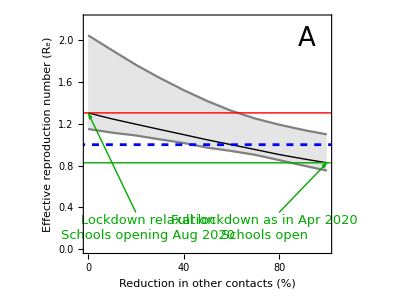

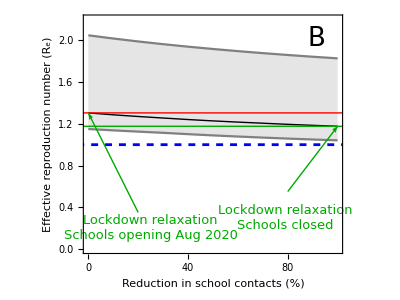

{{ManuscriptExit//Figures//Fig6A.pdf,ManuscriptExit//Figures//Fig6B.pdf},{ManuscriptExit//Figures//Fig6A.eps,ManuscriptExit//Figures//Fig6B.eps}}

```mathematica
Med={1.3048397698710397,1.24741768983246,1.1963530984363513,1.1460004263529067,1.0964938166820004,1.0460822159684269,0.9999217634271105,0.953125527828441,0.9053682578350881,0.8645281887676188,0.8260448787498277};
Quant1={1.150153799872694,1.1155021776784868,1.0881130234034755,1.0509346320956419,1.0161559695971758,0.9712303053230964,0.9393261427421087,0.9023609922667686,0.8520042539174039,0.8002265158370037,0.750782584122452};
Quant2={2.0492026590735333,1.9064220463213526,1.7663072733613103,1.6403464019209248,1.5236573338504247,1.417738572632495,1.3249757637579391,1.2505975800141065,1.1920641165712773,1.1417800882333344,1.098732209286168};

fig[1]=Show[ListLinePlot[{Med,Quant1,Quant2},
AspectRatio->0.75,ImageSize->400,PlotRangePadding->None,PlotRange->{{1,11},{0,2.2 }},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Effective reproduction number (R_e)",None},{"Reduction in other contacts (%)",None}},PlotStyle->{{Black,Thick},Gray,Gray},Filling->{3->{2}},FrameTicks->{{Automatic,None},{{{1,"0"},{3,"20"},{5,"40"},{7,"60"},{9,"80"},{11,"100"}},None}}],Graphics[{Thickness[0.005],Blue,Dashed,Line[{{0,1},{100,1}}]}],Graphics[{Thickness[0.0025],Red,Line[{{0,First[Med]},{100,First[Med]}}]}],
Graphics[{Thickness[0.0025],Darker[Green],Line[{{0,Last[Med]},{100,Last[Med]}}]}],Graphics[{Darker[Green],Arrow[{{9,0.35},{11,Last[Med]}}]}],
Graphics[Text[StyleForm["Full lockdown as in Apr 2020\nSchools open",FontSize->13,FontColor-> Darker[Green]],{8.4,0.2}]],Graphics[{Darker[Green],Arrow[{{3,0.35},{1,First[Med]}}]}],
Graphics[Text[StyleForm["Lockdown relaxation\nSchools opening Aug 2020",FontSize->13,FontColor-> Darker[Green]],{3.5,0.2}]],Graphics[Text[StyleForm["A",FontSize->26],Scaled[{0.9,0.9}]]]]


Med={1.3048397698710397,1.2864228675829774,1.2703772850468056,1.2556596430375488,1.2411989001127652,1.2280662379816958,1.2165669991506127,1.2058855974826883,1.1950890458086199,1.1855686378615726,1.1766051963404482};Quant1={1.150153799872694,1.1372476776237208,1.1252256159125884,1.1136637595268053,1.1008453479217106,1.0890060170700755,1.0780512441002479,1.0678930599298153,1.0584507123229374,1.0496508519578396,1.0414273834577528};Quant2={2.0492026590735333,2.0184435771596885,1.9901462719747167,1.9640901711234662,1.940059313014777,1.9178482230857072,1.8972656466712472,1.8781365199005835,1.860302613023825,1.8436222506322433,1.8279694436447738};

fig[2]=Show[ListLinePlot[{Med,Quant1,Quant2},
AspectRatio->0.75,ImageSize->400,PlotRangePadding->None,PlotRange->{{1,11},{0,2.2}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Effective reproduction number (R_e)",None},{"Reduction in school contacts (%)",None}},PlotStyle->{{Black,Thick},Gray,Gray},Filling->{3->{2}},FrameTicks->{{Automatic,None},{{{1,"0"},{3,"20"},{5,"40"},{7,"60"},{9,"80"},{11,"100"}},None}}],Graphics[{Thickness[0.005],Blue,Dashed,Line[{{0,1},{100,1}}]}],Graphics[{Thickness[0.0025],Red,Line[{{0,First[Med]},{100,First[Med]}}]}],Graphics[{Thickness[0.0025],Darker[Green],Line[{{0,Last[Med]},{100,Last[Med]}}]}],Graphics[{Darker[Green],Arrow[{{9,0.55},{11,Last[Med]}}]}],
Graphics[Text[StyleForm["Lockdown relaxation\nSchools closed",FontSize->13,FontColor-> Darker[Green]],{8.9,0.3}]],Graphics[{Darker[Green],Arrow[{{3,0.35},{1,First[Med]}}]}],
Graphics[Text[StyleForm["Lockdown relaxation\nSchools opening Aug 2020",FontSize->13,FontColor-> Darker[Green]],{3.5,0.2}]],Graphics[Text[StyleForm["B",FontSize->26],Scaled[{0.9,0.9}]]]]

FigNames={"A","B"};

Table[Export[StringJoin["ManuscriptExit//Figures//Fig6",FigNames⟦j⟧,format⟦i⟧],fig[j]],{i,1,Length[format]},{j,1,Length[FigNames]}]
```

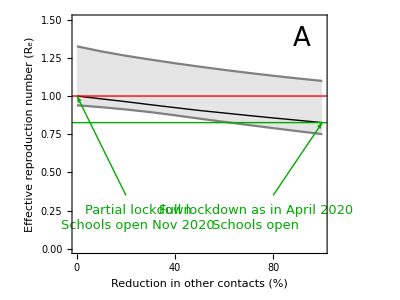

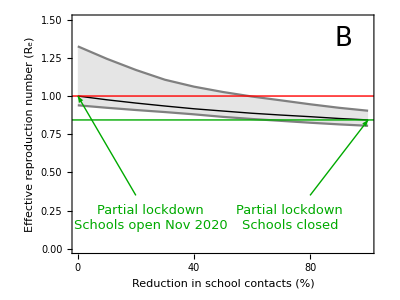

{{ManuscriptExit//Figures//Fig7A.pdf,ManuscriptExit//Figures//Fig7B.pdf},{ManuscriptExit//Figures//Fig7A.eps,ManuscriptExit//Figures//Fig7B.eps}}

```mathematica
Med={0.9999217634271105,0.9813865917582371,0.9629396554880858,0.9431891988271097,0.9241949129995476,0.9053682578350881,0.8891075193519458,0.87251138494793,0.8567538625717239,0.8415892573160485,0.8260448787498277};
Quant1={0.9393261427421087,0.9270029717901035,0.9119443245867818,0.8947084112877826,0.8739589297087678,0.8520042539174039,0.8310544396044907,0.8104166264887677,0.790129147717846,0.7702351142375139,0.750782584122452};Quant2={1.3249757637579391,1.2919030277311012,1.263341940322805,1.2382020740066273,1.2144507793410093,1.1920641165712773,1.171002977106597,1.1512153843210875,1.1326392833542966,1.1152055091362598,1.098732209286168};

AspRat=0.75; ImSize=400;

fig[1]=Show[ListLinePlot[{Med,Quant1,Quant2},
AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{1,11},{0,1.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Effective reproduction number (R_e)",None},{"Reduction in other contacts (%)",None}},PlotStyle->{{Black,Thick},Gray,Gray},Filling->{3->{2}},FrameTicks->{{Automatic,None},{{{1,"0"},{3,"20"},{5,"40"},{7,"60"},{9,"80"},{11,"100"}},None}}],Graphics[{Thickness[0.0025],Darker[Green],Line[{{0,Last[Med]},{100,Last[Med]}}]}],Graphics[{Thickness[0.0025],Red,Line[{{0,1},{100,1}}]}],Graphics[{Darker[Green],Arrow[{{9,0.35},{11,Last[Med]}}]}],
Graphics[Text[StyleForm["Full lockdown as in April 2020\nSchools open",FontSize->13,FontColor-> Darker[Green]],{8.3,0.2}]],Graphics[{Darker[Green],Arrow[{{3,0.35},{1,1}}]}],
Graphics[Text[StyleForm["Partial lockdown\nSchools open Nov 2020",FontSize->13,FontColor-> Darker[Green]],{3.5,0.2}]],Graphics[Text[StyleForm["A",FontSize->26],Scaled[{0.9,0.9}]]]]

Med={0.9999217634271105,0.9753938500332698,0.9540343905107305,0.9347212205461826,0.9166276380421526,0.9018281124342831,0.887370102990934,0.8755758231732893,0.8649501681666655,0.8530694899279043,0.8435648040190449};Quant1={0.9393261427421087,0.9230987735312871,0.9085210665649477,0.8951094027918945,0.8803204824526007,0.863608701821369,0.8498040542035785,0.837606685084576,0.8254292996374677,0.8145949051941861,0.8052822021643855};Quant2={1.3249757637579391,1.2435050730948312,1.1705832307498594,1.1066052569929972,1.0613478205156848,1.0263455227149951,0.9967406419010776,0.9716644905168057,0.9461402260322833,0.9229961757949166,0.9037751111992438};

fig[2]=Show[ListLinePlot[{Med,Quant1,Quant2},
AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{1,11},{0,1.5 }},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Effective reproduction number (R_e)",None},{"Reduction in school contacts (%)",None}},PlotStyle->{{Black,Thick},Gray,Gray},Filling->{3->{2}},FrameTicks->{{Automatic,None},{{{1,"0"},{3,"20"},{5,"40"},{7,"60"},{9,"80"},{11,"100"}},None}}],Graphics[{Thickness[0.0025],Darker[Green],Line[{{0,Last[Med]},{100,Last[Med]}}]}],Graphics[{Thickness[0.0025],Thickness[0.0025],Red,Line[{{0,1},{100,1}}]}],Graphics[{Darker[Green],Arrow[{{9,0.35},{11,Last[Med]}}]}],
Graphics[Text[StyleForm["Partial lockdown\nSchools closed",FontSize->13,FontColor-> Darker[Green]],{8.3,0.2}]],Graphics[{Darker[Green],Arrow[{{3,0.35},{1,1}}]}],
Graphics[Text[StyleForm["Partial lockdown\nSchools open Nov 2020",FontSize->13,FontColor-> Darker[Green]],{3.5,0.2}]],Graphics[Text[StyleForm["B",FontSize->26],Scaled[{0.9,0.9}]]]]

FigNames={"A","B"};

Table[Export[StringJoin["ManuscriptExit//Figures//Fig7",FigNames⟦j⟧,format⟦i⟧],fig[j]],{i,1,Length[format]},{j,1,Length[FigNames]}]
```

```mathematica
ReffRange[Intervention_]:=Block[{JacobAnalyt,JacobAnalytDiseaseFreeState,TransmissionMatrix,TransitionMatrix,Reffvals},
JacobAnalyt=Table[ D[EqsList[Intervention]⟦k,2⟧,VarsList⟦p⟧],{k,EqNumbersR0} ,{p,EqNumbersR0}];
JacobAnalytDiseaseFreeState=JacobAnalyt/.DiseaseFreeState;
TransmissionMatrix=ϵ Table[Coefficient[JacobAnalytDiseaseFreeState⟦k⟧⟦p⟧,ϵ],{k,1,Length[EqNumbersR0]} ,{p,1,Length[EqNumbersR0]}];
TransitionMatrix=JacobAnalytDiseaseFreeState-TransmissionMatrix;
(*Print[Style["Effective reproduction number",18,Blue,"Text"]];*)
Print[Style[Intervention,18,Blue,"Text"]];

Table[Re[Eigenvalues[(-TransmissionMatrix/.Join[Parameters[i],{ω->j,κ->0.67,pp->0.8}]).Inverse[TransitionMatrix/.Join[Parameters[i],{ω->j,κ->0.67,pp->0.8}]]]⟦1⟧],{i,1,NumSamples,10},{j,1,0,-0.1}]

]
```

```mathematica
Print[Style["R_e, Median, 2.5% Quantile, 97.5% Quantile, Mean, Standard Deviation",18,Blue,"Text"]]
Reffvals1=ReffRange["Relaxation with Schools 1"];
PrintStats[Reffvals1]

Reffvals2=ReffRange["Relaxation with Schools 2"];
PrintStats[Reffvals2]

Reffvals3=ReffRange["Relaxation with Schools 3"];
PrintStats[Reffvals3]
```

R_e, Median, 2.5% Quantile, 97.5% Quantile, Mean, Standard Deviation

Relaxation with Schools 1

{{0.999922,0.999318,0.998716,0.998117,0.99752,0.996925,0.996332,0.995731,0.995092,0.994456,0.993823},{0.939326,0.938836,0.938348,0.937862,0.937377,0.936894,0.936413,0.935934,0.935456,0.93498,0.934506},{1.32498,1.32443,1.32388,1.32334,1.32281,1.32227,1.32175,1.32122,1.3207,1.32019,1.31968},{1.0272,1.02658,1.02597,1.02536,1.02475,1.02415,1.02355,1.02295,1.02236,1.02176,1.02117},{0.0984045,0.0983955,0.0983872,0.0983797,0.0983729,0.0983668,0.0983615,0.0983568,0.0983528,0.0983495,0.0983469}}

Relaxation with Schools 2

{{0.999922,0.991521,0.984228,0.97689,0.971251,0.96633,0.962248,0.958428,0.954779,0.951393,0.948436},{0.939326,0.934519,0.928783,0.924394,0.920476,0.916961,0.91379,0.910916,0.908299,0.905905,0.903705},{1.32498,1.2918,1.26559,1.24499,1.2287,1.21569,1.20515,1.19649,1.18927,1.18317,1.17796},{1.0272,1.01646,1.00739,0.999697,0.993111,0.987425,0.982472,0.978118,0.97426,0.970814,0.967715},{0.0984045,0.0921064,0.0872418,0.0835132,0.0806518,0.0784408,0.0767151,0.0753525,0.074264,0.0733843,0.0726655}}

Relaxation with Schools 3

{{0.999922,0.987468,0.976102,0.965318,0.956612,0.947609,0.939973,0.933367,0.927126,0.921302,0.916001},{0.939326,0.931899,0.922641,0.915371,0.908717,0.902611,0.896994,0.891811,0.886703,0.881394,0.876471},{1.32498,1.29059,1.26171,1.23768,1.21775,1.20118,1.18735,1.1757,1.16582,1.15735,1.15002},{1.0272,1.01265,0.999698,0.988171,0.977895,0.968705,0.960453,0.953011,0.946268,0.940128,0.93451},{0.0984045,0.092291,0.0872838,0.0832472,0.0800276,0.0774754,0.0754576,0.0738631,0.0726018,0.0716027,0.0708102}}

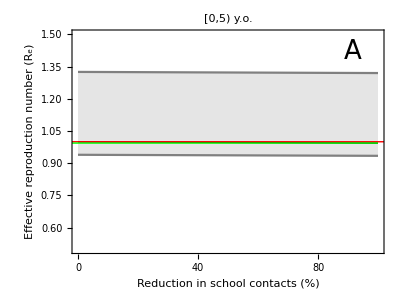

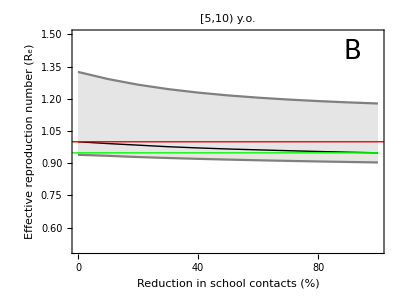

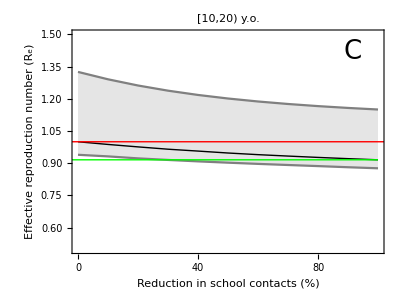

{{ManuscriptExit//Figures//Fig8A.pdf,ManuscriptExit//Figures//Fig8B.pdf,ManuscriptExit//Figures//Fig8C.pdf},{ManuscriptExit//Figures//Fig8A.eps,ManuscriptExit//Figures//Fig8B.eps,ManuscriptExit//Figures//Fig8C.eps}}

```mathematica
AspRat=0.75; ImSize=400;

figschools[1]=Show[ListLinePlot[{Median[Reffvals1],Quantile[Reffvals1,0.025],Quantile[Reffvals1,0.975]},
AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{1,11},{0.5,1.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Effective reproduction number (R_e)",None},{"Reduction in school contacts (%)",None}},PlotStyle->{{Black,Thick},Gray,Gray},Filling->{3->{2}},FrameTicks->{{Automatic,None},{{{1,"0"},{3,"20"},{5,"40"},{7,"60"},{9,"80"},{11,"100"}},None}},PlotLabel->Style[Row[{"[0,5) y.o."}],Black,17]],Graphics[{Thickness[0.0025],Red,Line[{{0,1},{100,1}}]}],Graphics[{Thickness[0.0025],Green,Line[{{0,Last[Median[Reffvals1]]},{11,Last[Median[Reffvals1]]}}]}],Graphics[Text[StyleForm["A",FontSize->26],Scaled[{0.9,0.9}]]]]

figschools[2]=Show[ListLinePlot[{Median[Reffvals2],Quantile[Reffvals2,0.025],Quantile[Reffvals2,0.975]},
AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{1,11},{0.5,1.5}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Effective reproduction number (R_e)",None},{"Reduction in school contacts (%)",None}},PlotStyle->{{Black,Thick},Gray,Gray},Filling->{3->{2}},FrameTicks->{{Automatic,None},{{{1,"0"},{3,"20"},{5,"40"},{7,"60"},{9,"80"},{11,"100"}},None}},PlotLabel->Style[Row[{"[5,10) y.o."}],Black,17]],Graphics[{Thickness[0.0025],Red,Line[{{0,1},{100,1}}]}],Graphics[{Thickness[0.0025],Green,Line[{{0,Last[Median[Reffvals2]]},{11,Last[Median[Reffvals2]]}}]}],Graphics[Text[StyleForm["B",FontSize->26],Scaled[{0.9,0.9}]]]]

figschools[3]=Show[ListLinePlot[{Median[Reffvals3],Quantile[Reffvals3,0.025],Quantile[Reffvals3,0.975]},
AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{1,11},{0.5,1.5}},AxesOrigin->{0,0},Filling->{3->{2}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Effective reproduction number (R_e)",None},{"Reduction in school contacts (%)",None}},PlotStyle->{{Black,Thick},Gray,Gray},FrameTicks->{{Automatic,None},{{{1,"0"},{3,"20"},{5,"40"},{7,"60"},{9,"80"},{11,"100"}},None}},PlotLabel->Style[Row[{"[10,20) y.o."}],Black,17]],Graphics[{Thickness[0.0025],Red,Line[{{0,1},{100,1}}]}],Graphics[{Thickness[0.0025],Green,Line[{{0,Last[Median[Reffvals3]]},{11,Last[Median[Reffvals3]]}}]}],Graphics[Text[StyleForm["C",FontSize->26],Scaled[{0.9,0.9}]]]]

FigNames={"A","B","C"};

Table[Export[StringJoin["ManuscriptExit//Figures//Fig8",FigNames⟦j⟧,format⟦i⟧],figschools[j]],{i,1,Length[format]},{j,1,Length[FigNames]}]
```

```mathematica
red1=(First[Median[Reffvals1]]-Last[Median[Reffvals1]])/First[Median[Reffvals1]] 100
red2=(First[Median[Reffvals2]]-Last[Median[Reffvals2]])/First[Median[Reffvals2]] 100
red3=(First[Median[Reffvals3]]-Last[Median[Reffvals3]])/First[Median[Reffvals3]] 100

red1+red2+red3

red={0.9999217634271105,0.9753938500332698,0.9540343905107305,0.9347212205461826,0.9166276380421526,0.9018281124342831,0.887370102990934,0.8755758231732893,0.8649501681666655,0.8530694899279043,0.8435648040190449};

(First[red]-Last[red])/First[red] 100

red={1.3048397698710397,1.2864228675829774,1.2703772850468056,1.2556596430375488,1.2411989001127652,1.2280662379816958,1.2165669991506127,1.2058855974826883,1.1950890458086199,1.1855686378615726,1.1766051963404482};
(First[red]-Last[red])/First[red] 100
```

0.609955

5.14893

8.39271

14.1516

15.6369

9.82761

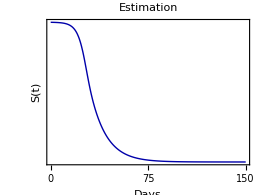
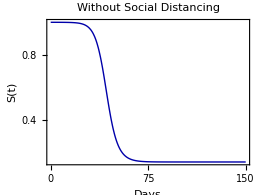
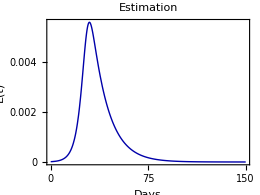
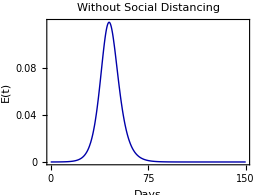
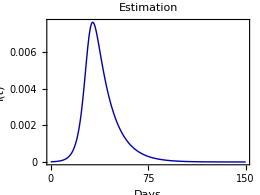
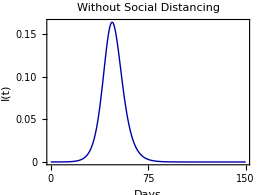
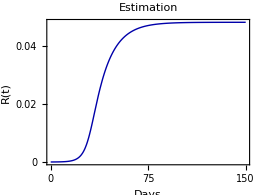
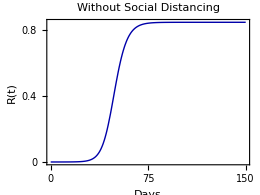

```mathematica
Subscript[t, start]=0;
Subscript[t, end]=150;

ICs=Table[ic[j,k],{j,VarNumbers},{k,AgeGroups}];
ICsList=Flatten[Flatten[ICs]];
Dimensions[ICsList];

Table[ic[1,k]=Subscript[S0,k] Subscript[NN,k]==Subscript[S,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[2,k]=Subscript[EE0,k] Subscript[NN,k]==Subscript[EE,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[3,k]=Subscript[II0,k,1] Subscript[NN,k]==Subscript[II,k,1][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[4,k]=Subscript[II0,k,2] Subscript[NN,k]==Subscript[II,k,2][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[5,k]=Subscript[II0,k,NumInfStages] Subscript[NN,k]==Subscript[II,k,NumInfStages][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[6,k]=Subscript[R0,k] Subscript[NN,k]==Subscript[R,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[7,k]=Subscript[H0,k] Subscript[NN,k]==Subscript[H,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];

solution[Intervention_]:=NDSolve[Join[EqsList[Intervention],ICsList]/.ParametersMAP(*Join[ParametersMAP,{x1-> 70,K1-> 0.75,κ-> 0.25}]*),VarsList,{t,Subscript[t, start],Subscript[t, end]} ];

(*sol=solution[Intervention];*)

intList={"Estimation","Without Social Distancing"};

Table[sol[it]=solution[intList⟦it⟧],{it,1,Length[intList]}];

AspRat=0.75;
ImSize=260;

totVarsYlab={"S(t)","E(t)","I(t)","R(t)","H(t)"};

Transpose[Table[Table[fig7[i,it]=Plot[Evaluate[(totVars⟦i⟧/NNtot/.ParametersMAP(*Join[ParametersMAP,{x1-> 70,K1-> 0.75,κ->0.25}]*))/.sol[it]],{t,Subscript[t, start],Subscript[t, end]},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},{0,All}},PlotStyle->{Thick,Darker[Blue]},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},PlotTheme-> "Web",FrameStyle->Directive[Black,17],PlotLabel->Style[Row[{intList⟦it⟧}],Black,17],FrameLabel-> {{totVarsYlab⟦i⟧,None},{"Days",None}}],{i,1,Length[totVars]}],{it,1,Length[intList]}]]

(*Table[Export[StringJoin["ManuscriptExit//Figures//Fig7_",ToString[i],ToString[it],format⟦j⟧],fig7[i,it]],{j,1,Length[format]},{i,1,Length[totVars]},{it,1,Length[intList]}]*)
```

## Prevalence of individuals in different classes per age group MAP parameter sample

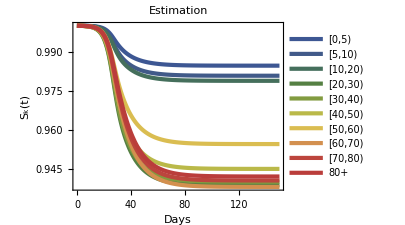
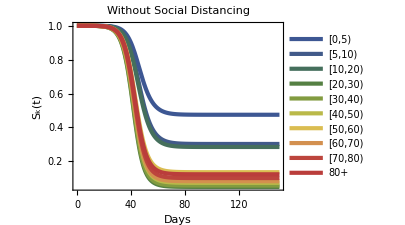
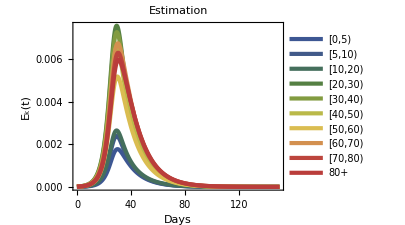
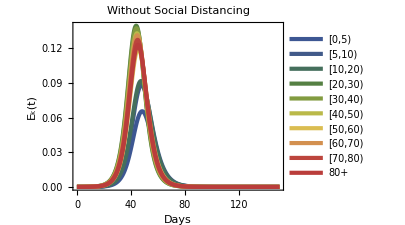
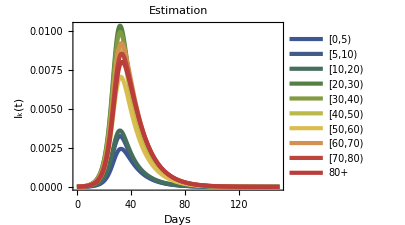
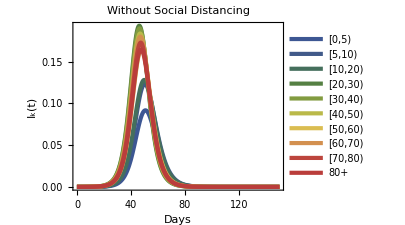
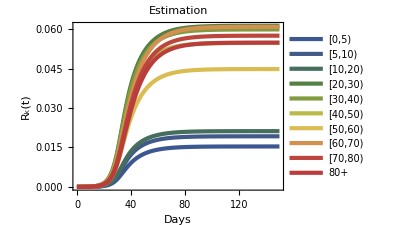
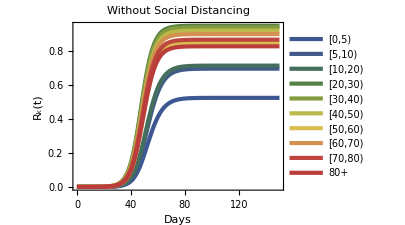

```mathematica
ageVars={Subscript[S,k][t],Subscript[EE,k][t],Subscript[II,k][t],Subscript[R,k][t],Subscript[H,k][t]};
ageVarsYlab={"S_k(t)","E_k(t)","I_k(t)","R_k(t)","H_k(t)"};

Transpose[Table[Table[fig8[i,it]=Plot[
Evaluate[Table[(ageVars⟦i⟧/Subscript[NN,k]/.ParametersMAP)/.sol[it],{k,AgeGroups}]],{t,Subscript[t, start],Subscript[t, end]},AspectRatio->AspRat,ImageSize->300,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},{0,All}},PlotStyle->"DarkRainbow",AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotLabel->Style[Row[{intList⟦it⟧}],Black,17],FrameLabel-> {{ageVarsYlab⟦i⟧,None},{"Days",None}},PlotTheme-> "Web",PlotLegends->Placed[{"[0,5)","[5,10)","[10,20)","[20,30)","[30,40)","[40,50)","[50,60)","[60,70)","[70,80)","80+"},Right]],{i,1,Length[ageVars]}],{it,1,Length[intList]}]]

(*Table[Export[StringJoin["ManuscriptExit//Figures//Fig8_",ToString[i],ToString[it],format⟦j⟧],fig8[i,it]],{j,1,Length[format]},{i,1,Length[totVars]},{it,1,Length[intList]}]*)
```

## Cumulative hospitalizations in 8 classes MAP parameter sample

```mathematica
HospitalisationsData=Import["hospitalisations_selected.csv"];
HospitalisationsData=Drop[HospitalisationsData,1];
Dimensions[HospitalisationsData]
TableForm[HospitalisationsData];

hospVars={Subscript[ν,1] Subscript[II,1][t]+Subscript[ν,2] Subscript[II,2][t]+Subscript[ν,3] Subscript[II,3][t],Subscript[ν,4] Subscript[II,4][t],Subscript[ν,5] Subscript[II,5][t],Subscript[ν,6] Subscript[II,6][t],Subscript[ν,7] Subscript[II,7][t],Subscript[ν,8] Subscript[II,8][t],Subscript[ν,9] Subscript[II,9][t],Subscript[ν,10] Subscript[II,10][t]};

hospVarsYlab={"Hospitalizations","Hospitalizations","Hospitalizations","Hospitalizations","Hospitalizations","Hospitalizations","Hospitalizations","Hospitalizations"};

AgeLabel={"[0,20) y.o.","[20,30) y.o.","[30,40) y.o.","[40,50) y.o.", "[50,60) y.o.","[60,70) y.o.","[70,80) y.o.","80+ y.o."};

hospDataGrouped[1]=HospitalisationsData⟦All,1⟧+HospitalisationsData⟦All,2⟧+HospitalisationsData⟦All,3⟧;
hospDataGrouped[2]=HospitalisationsData⟦All,4⟧;
hospDataGrouped[3]=HospitalisationsData⟦All,5⟧;
hospDataGrouped[4]=HospitalisationsData⟦All,6⟧;
hospDataGrouped[5]=HospitalisationsData⟦All,7⟧;
hospDataGrouped[6]=HospitalisationsData⟦All,8⟧;
hospDataGrouped[7]=HospitalisationsData⟦All,9⟧;
hospDataGrouped[8]=HospitalisationsData⟦All,10⟧;


NumHospGroups={1,2,3,4,5,6,7,8};
```

{69,10}

# Solutions with credible intervals

## Hospitalizations incidence in 8 classes CrI based on 1000 samples

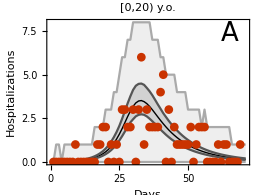
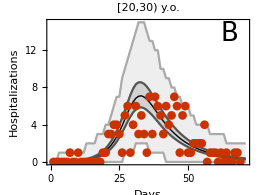
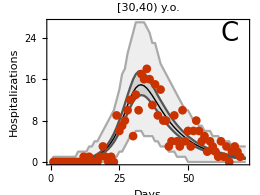
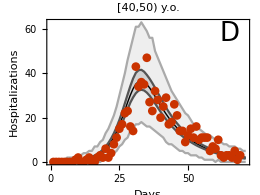
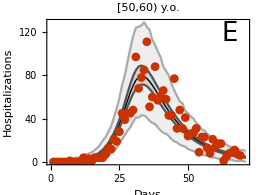
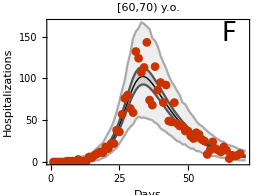
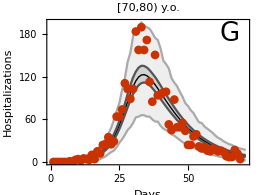
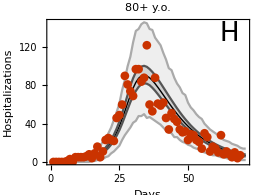

{{ManuscriptExit//Figures//Fig2A.pdf,ManuscriptExit//Figures//Fig2B.pdf,ManuscriptExit//Figures//Fig2C.pdf,ManuscriptExit//Figures//Fig2D.pdf,ManuscriptExit//Figures//Fig2E.pdf,ManuscriptExit//Figures//Fig2F.pdf,ManuscriptExit//Figures//Fig2G.pdf,ManuscriptExit//Figures//Fig2H.pdf},{ManuscriptExit//Figures//Fig2A.eps,ManuscriptExit//Figures//Fig2B.eps,ManuscriptExit//Figures//Fig2C.eps,ManuscriptExit//Figures//Fig2D.eps,ManuscriptExit//Figures//Fig2E.eps,ManuscriptExit//Figures//Fig2F.eps,ManuscriptExit//Figures//Fig2G.eps,ManuscriptExit//Figures//Fig2H.eps}}

```mathematica
Subscript[t, start]=0;
Subscript[t, end]=Dimensions[HospitalisationsData]⟦1⟧+2;
Subscript[t, step]=1;

solutionCrI[Intervention_,sample_]:=NDSolve[Join[EqsList[Intervention],ICsList]/.Parameters[sample],VarsList,{t,Subscript[t, start],Subscript[t, end]} ];

nSamples=Dimensions[EstimatesData]⟦1⟧;
stepSamples=1;
ListSamples=Table[i,{i,1,nSamples,stepSamples}];

Trajectories[Intervention_,vars_]:=Table[Transpose[{Table[t,{t,Subscript[t, start],Subscript[t, end]}],Table[Evaluate[(vars/.Parameters[i])/.First@solutionCrI[Intervention,i]],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}]}],{i,1,nSamples,stepSamples}];

HospIncidence=Table[Trajectories["Estimation",hospVars⟦k⟧],{k,NumHospGroups}];

HospIncidenceSimulated=HospIncidence;

(* 
formattable={".csv",".txt",".dat",".xlsx",".tsv"};
Table[Export[StringJoin["ManuscriptExit//Figures//HospIncidence",formattable⟦j⟧],HospIncidence,"Table"],{j,1,Length[formattable]}];
*)
NBDReparameterized[m_,f_]:=NegativeBinomialDistribution[f,f/(f+m)];
Table[If[HospIncidenceSimulated⟦k⟧⟦sample⟧⟦t,2⟧>0,HospIncidenceSimulated⟦k⟧⟦sample⟧⟦t,2⟧=RandomVariate[NBDReparameterized[HospIncidenceSimulated⟦k⟧⟦sample⟧⟦t,2⟧,rOverDisp[ListSamples⟦sample⟧]]]],{k,1,Dimensions[HospIncidenceSimulated]⟦1⟧},{sample,1,Dimensions[HospIncidenceSimulated]⟦2⟧},{t,1,Dimensions[HospIncidenceSimulated]⟦3⟧}];

FigNames={"A","B","C","D","E","F","G","H"};

Table[fig9[k]=Show[
ListLinePlot[{Median[HospIncidence⟦k⟧],Quantile[HospIncidence⟦k⟧,0.025],Quantile[HospIncidence⟦k⟧,0.975],Quantile[HospIncidenceSimulated⟦k⟧,0.025],Quantile[HospIncidenceSimulated⟦k⟧,0.975]},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},All},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{hospVarsYlab⟦k⟧,None},{"Days",None}},Filling->{{3->{2}},{5-> {4}}},PlotStyle->{{Black,Thick},Darker[Gray],Darker[Gray],Lighter[Gray],Lighter[Gray]},PlotLabel->Style[Row[{AgeLabel⟦k⟧}],Black,17]],
ListPlot[hospDataGrouped[k],PlotMarkers->Automatic,PlotTheme->"Web"],Graphics[Text[StyleForm[FigNames⟦k⟧,FontSize->26],Scaled[{0.9,0.9}]]]
],{k,NumHospGroups}]

Table[Export[StringJoin["ManuscriptExit//Figures//Fig2",FigNames⟦k⟧,format⟦j⟧],fig9[k]],{j,1,Length[format]},{k,NumHospGroups}]
```